```mathematica
SetDirectory["/Users/haneeshkesari"]
```

/Users/haneeshkesari

```mathematica
ClearAll[f]
f[x_]:=Module[{strs,str},
str=RunProcess[{"a.out",ToString[DecimalForm[x]],100},"StandardOutput"];
strs=StringSplit[str,"E"];
If[Length[strs]>1,ToExpression[strs[[1]]]*10^ToExpression[strs[[2]]],ToExpression[strs[[1]]]]]


ClearAll[GFortran]
GFortran[inp_]:=Module[{output},
RunProcess[{"rm","temp1.f90","a.out"}]//Echo;
Export["temp1.f90",inp,"Text"]//Echo;
RunProcess[{"/usr/local/bin/gfortran","temp1.f90"}]//Echo
(*output=RunProcess["a.out","StandardOutput"];
output*)
];
```

```mathematica
ClearAll[pr]
pr="PROGRAM test
implicit none
Character(300):: N_char, x_char
Integer::b,i, N=100
Real, parameter :: PI=3.14
Real(kind=16) :: x=10e-10, ans=0.0, N_real=0.0
Call getarg(1, x_char)
Call getarg(2, N_char)
Read(x_Char,*)x
Read(N_Char,*)N_real; N=nint(N_real)


! print*, 'N_char is ', N_char
! print*, 'x_Char is ', x_char
! print*, 'x is ', x
! print*, 'N is ', N

! do i=0,N
!   ! print*, ans
! \tans=ans+(x**i)/Gamma(Real(i+1))
! end do

ans=Gamma(x)**2



print*, ans

END Program test
";
GFortran[pr];
```

<|ExitCode→0,StandardOutput→,StandardError→|>

temp1.f90

<|ExitCode→0,StandardOutput→,StandardError→|>

```mathematica
(*RunProcess[{"/usr/local/bin/gfortran","temp1.f90"}]//Echo;*)
```

```mathematica
Block[{x=2},
f[N[x]]//Echo;
(Gamma[x]^2)//N//Echo;]
```

1.

1.

```mathematica
FileNames[]//TableForm
```

0x7fe06ec02680.1910
.anaconda
anaconda3
Applications
.atom
.atom_exp
.atom_original
.aws
.bash_history
.bash_profile
.bash_sessions
bin
.cabal
.cache
.cacher
C_Cpp_Petsc
.CFUserTextEncoding
.cling_history
.cmake
Computational-Solid-Mechanics
.conda
conda
.condarc
.config
Creative Cloud Files
.cups
Data
dead.letter
Desktop
.docker
Documents
Downloads
.dropbox
Dropbox (Brown)
DropboxBrown
.DS_Store
dumnmy
.emacs.d
.enhancd
enhancd
file.ext
.ghc
.ghcup
.gitconfig
.gitlab-runner
.gmshrc
.gnuplot_history
.histdb
.hunter
.idlerc
.ihaskell
.ipynb_checkpoints
.ipython
.julia
June23_2020.rtf
.jupyter
.kite
.lesshst
Library
.local
.macports
mathematical-python
.matplotlib
mbox
.mono
Movies
Music
.ne
.netrc
.ngrok2
.npm
.oh-my-zsh
OneDrive
.openjfx
opt
OpticsMechanicsExperiments
.oracle_jre_usage
petsc
Pictures
Public
.pyenv
.pylint.d
.python_history
.python-version
.pywren_config
.root_hist
.rootnb
.shell.pre-oh-my-zsh
.spyder-py3
.ssh
.stack
.swp
test.bbl
test.blg
test.f90
test.hs
test.txt
.textadept
.Trash
.vcpkg
.vim
.viminfo
.vscode
.wget-hsts
.Xauthority
.zcompdump-Haneeshs-MacBook-Pro-2-5.7.1
.zcompdump-Haneesh’s MacBook Pro (2)-5.3
.zcompdump-Haneesh’s MacBook Pro (2)-5.7.1
.zprofile
.zprofile.macports-saved_2020-01-22_at_12:22:59
.zsh_history
.zshrc
.zshrc~
.zshrc (original)

```mathematica
f[3.14]
```

RunProcess::pnfd: Program a.out not found.  Check Environment["PATH"].

StringSplit::strse: String or list of strings expected at position 1 in StringSplit[$Failed,E].

10^ⅇ $Failed

-1.

```mathematica
Factorial[x]//FortranForm
```

Factorial(x)

```mathematica
f[x_]:=RunProcess[{"a.out",x,100},"StandardOutput"]//StringToStream//Read[#,Real] &
(*RunProcess[$SystemShell,"StandardOutput","a.out 1
exit
"]*)
```

```mathematica
Plot[{f[x],Exp[x]},{x,0,.0001},PlotRange->All,PlotStyle->{Red,Dashed}]
```

```mathematica
f[1.0000001]
```

2.7182818284590452356031470605690172

```mathematica
f[0.1]
```

1.105170918075647624811707826490249

```mathematica
RunProcess[{"a.out",10,100},"StandardOutput"]
```

```mathematica
f[10]
```

Read::readn: Invalid real number found when reading from StringToStream[ N_char is100                             
 x is    10.000000000000000000000000…98596581841947995282438027      
   22026.4657798596581841947995282438027      
].

$Failed

```mathematica
f[3]
```

Read::readn: Invalid real number found when reading from StringToStream[              NaN
].

$Failed

```mathematica
ListPlot[{x,f[x]},{x,Range[100]}]
```

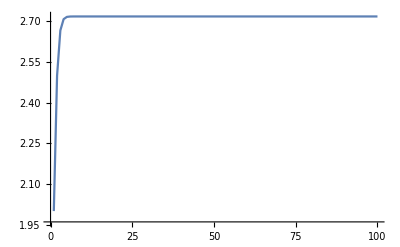

```mathematica
{#,f[#]}&/@Range[100]
ListLinePlot[%]
```

```mathematica
Directory[]
```

/Users/haneeshkesari

1.001

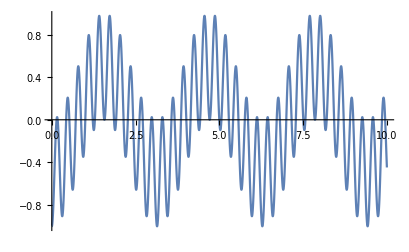

```mathematica
ListLinePlot[ParallelMap[{#,f[#]} &,Range[0,10,0.001]](*,PlotStyle->{{Thickness[0.02],Yellow,Opacity[0.8],Dashed},{Black}}*)]
```

```mathematica
Block[{x},
f[x]//Echo;
(*f["10e-7"]*)
(Sin[x]^2-Cos[10 x]^2)//N//Echo;]
```

0.044811723191593952076394665641581135

0.0448117

```mathematica
f[10]
```

NaN

```mathematica
f[0.0000001]
```

0.030538177898217311805001588420672991

4.03238736687520046765018428655844369E-0003

```mathematica
str=RunProcess[{"a.out",ToString[0.0000001],100},"StandardOutput"]
```

3.05381778982173118050015884206729906E-0002

```mathematica
strs=StringSplit[str,"E"];
If[Length[strs]>1,ToExpression[strs[[1]]]*10^ToExpression[strs[[2]]],ToExpression[strs[[1]]]]]
```

```mathematica
f[0.0000001]
```

0.030538177898217311805001588420672991

0.0040323873668752004676501842865584437

```mathematica
strs[[2]]
```

Part::partw: Part 2 of { -0.447634868410198948208507881131084566      
} does not exist.

{ -0.447634868410198948208507881131084566      
}⟦2⟧

```mathematica
ToString["0.0000001"]
```

0.0000001

```mathematica
0.0000001
```

1.×10^-7

```mathematica
?ToString
```

```mathematica
DecimalForm[0.0000001]//ToString//
```

0.0000001

```mathematica
Table[{x,f[x]},{x,Range[0,10,0.01]}]//Timing
```

{33.5549,{{0.,-1.},{0.01,-0.98993329225390970476844605379282199},{0.02,-0.96013055033193151155654874509046814},{0.03,-0.91176807742244123139430709306910765},{0.04,-0.84675420782489240294922837813791815},{0.05,-0.76765323557308274174824929762342351},{0.06,-0.677583195165269914943235761740355},{0.07,-0.58009156955643905525784813110752502},{0.08,-0.47901388053716911141759103053591953},{0.09,-0.37832079904751717963802085904047605},{0.1,-0.28195987064704962206331414362370334},{0.11,-0.19369816603762989044094018419488392},{0.12,-0.1169721296553920526586765098142981},{0.13,-0.054750612382782995880257747402431878},{0.14,-0.0094165488210563976689009681151614822},{0.15,0.017328003737419718814631283581605697},{0.16,0.024529678856156108543176724258745467},{0.17,0.012021763525557392889778739869558346},{0.18,-0.019569203671893926240310321429400602},{0.19,-0.06884846183104677474798131668691625},{0.2,-0.13370868656963658407967927447702563},{0.21,-0.21141405948580434739027195414426693},{0.22,-0.29870939662077186702319882339032905},{0.23,-0.39194998529523536255324104113560876},{0.24,-0.48724695310936538186008504440411449},{0.25,-0.58062237367679949029146037705869353},{0.26,-0.66816792548901342951347074929857882},{0.27,-0.74620077865322925247236030894926904},{0.28,-0.81141049476183296187516758301180078},{0.29,-0.86099108342825296941127271490575295},{0.3,-0.89275295078002215889330239843915029},{0.31,-0.90521027684287570191170113911498045},{0.32,-0.89764033832124263609042493896624054},{0.33,-0.87011241172794727950177740644922059},{0.34,-0.82348510455037655481200936194529496},{0.35,-0.7593722208138965321985287559555234},{0.36,-0.68007852183657482522516872067283669},{0.37,-0.58850794315198927946276151469958613},{0.38,-0.48804792666158027619892055800940128},{0.39,-0.3824344792874634651244164683585179},{0.4,-0.27560333776927594752595429990556508},{0.41,-0.17153317315188917213303492695864391},{0.42,-0.074087085862311409388933098142697277},{0.43,0.013141289577980427296219560468309036},{0.44,0.086970934931537677436793449248615714},{0.45,0.14476014680700626594178927988701592},{0.46,0.18451173238035045007202031590071404},{0.47,0.20495250850205412110847880272444928},{0.48,0.20558393486083512394764563976593819},{0.49,0.18670186266926810883635974236464059},{0.5,0.14938461160415636742896367019054411},{0.51,0.095449850387775083719253473037174853},{0.52,0.027382000097225331629151018320638589},{0.53,-0.051766945544349119587787685689227808},{0.54,-0.13849922885920226494478842364144735},{0.55,-0.22901090970681408675986253825432871},{0.56,-0.31934365504773163270384997785214965},{0.57,-0.40554268515312433280812216732588927},{0.58,-0.4838145795871235320508813324531666},{0.59,-0.5506786516788599887473504092064015},{0.6,-0.60310585660458284114616432439834902},{0.61,-0.63863969519534228436767061819172612},{0.62,-0.65549429335881991001431707523649616},{0.63,-0.6526257469396470419671773135311787},{0.64,-0.62977388766469550787378544823545255},{0.65,-0.58747280503739181042533513238367358},{0.66,-0.52702970464641163817742680352758807},{0.67,-0.45047294568096389941824576503389928},{0.68,-0.3604713291722840326794965442787451},{0.69,-0.26022785462344100287756827304169095},{0.7,-0.15335218055403726643283845593769416},{0.71,-0.043716873493801651252195541335300024},{0.72,0.064696823737805000251067908468537109},{0.73,0.16795755579609819226656875054880232},{0.74,0.26234042924520527511885461585673476},{0.75,0.34447535559555918187997827609950585},{0.76,0.41148124903875064770379121608897671},{0.77,0.46108072890235702002342638317211157},{0.78,0.49169075406277388871987937524206761},{0.79,0.5024855760710484222693675850233198},{0.8,0.49342950131233668405270384779880103},{0.81,0.46527815613820239503494179624935426},{0.82,0.41954820459806643715634761080129704},{0.83,0.35845672609142304913560339615380384},{0.84,0.28483266982561716824140079452927924},{0.85,0.20200391617356080315399275694336825},{0.86,0.11366444750160155372312126502262398},{0.87,0.023726924010300732471721580074674704},{0.88,-0.063833458013180938136051138825045954},{0.89,-0.14513760058981552019848784300533103},{0.9,-0.21655730677549654474971286912993498},{0.91,-0.27486008016154481895153961704458882},{0.92,-0.31733814838789438731542312612596049},{0.93,-0.34191656684701437588479567323134332},{0.94,-0.34723609276368844680090386049921906},{0.95,-0.33270752566158291530975958073392359},{0.96,-0.29853534777298615658243654565283793},{0.97,-0.24570972186284819932275130254533484},{0.98,-0.1759671654286715755307514715169797},{0.99,-0.091721469012260148487502489421396631},{1.,0.0040323873668752004676501842865584437},{1.01,0.10783748916651924423788922248163767},{1.02,0.21591265940461518577409746019937222},{1.03,0.32430305937616766058747512523109345},{1.04,0.42903771408600005360676902026598342},{1.05,0.52628768241206293650260482833507479},{1.06,0.61251856631004690932825561585132218},{1.07,0.68463127905401871044123507870023632},{1.08,0.74008546058236685779324422953230792},{1.09,0.77700061982285664154870456079575396},{1.1,0.7942309718249914174891586759338112},{1.11,0.79141098623221840503684831323991691},{1.12,0.76896983127227013732760389971432628},{1.13,0.72811413748074617365713432403096175},{1.14,0.67077976836455936553155461903774294},{1.15,0.59955452080661087426681911416507152},{1.16,0.5175748369517554405635382709700351},{1.17,0.42840064539354479917962830828435354},{1.18,0.33587332139617574336369390724210728},{1.19,0.24396242887602338729511750743214426},{1.2,0.15660735410212426183588564128778819},{1.21,0.077560144725140869495427835933915251},{1.22,0.010235819690800067327686817297470908},{1.23,-0.042423882247704531486763437739521412},{1.24,-0.078067883459319881181073575967800748},{1.25,-0.09502959815826994162489596417428632},{1.26,-0.092393472145620196836285308564673118},{1.27,-0.070031578800463482501960791814841769},{1.28,-0.02860881231575135928547933293341951},{1.29,0.030443528896434179507739959218135189},{1.3,0.10498471552015344553815912487814988},{1.31,0.19224984606034911094782429463985658},{1.32,0.28895999201490557114073360033073123},{1.33,0.39145283838668985406965620943433743},{1.34,0.49582861134262594598860410912235953},{1.35,0.59810547537544867067696605889048015},{1.36,0.69437820480348691190738805397242926},{1.37,0.78097380390518233148088834950579013},{1.38,0.85459787163222303845994420727025998},{1.39,0.91246587582847344179040616923791011},{1.4,0.95241410349111237728112058763273141},{1.41,0.97298586386129045515848643495092065},{1.42,0.97348950772203844826345748924241258},{1.43,0.95402594987885518805696624552820105},{1.44,0.91548459760908188064149863196667203},{1.45,0.8595078474192954367731492308003365},{1.46,0.78842556553111843634649533377235224},{1.47,0.70516216416865647806991337018967767},{1.48,0.61311997823846398104424958149455218},{1.49,0.51604359182027482067658992669195036},{1.5,0.41787052335643070327645532405852558},{1.51,0.32257422226233824944102725583006049},{1.52,0.23400563619842457862037070934326097},{1.53,0.15573966522603034194315821931664448},{1.54,0.090932624243787842810582524030875054},{1.55,0.042196396234374092764970114195555676},{1.56,0.011494293440333597431745353053266651},{1.57,0.000062778159778376721950500698815721805},{1.58,0.0083621639100725490477429299607927459},{1.59,0.036058262350528383330319100150591717},{1.6,0.082035707644121406223067125706645064},{1.61,0.14444242705743959011317978787705422},{1.62,0.22076348489458829385605764801859862},{1.63,0.30792135583737884590645773064752748},{1.64,0.40239863010584228536308756051797216},{1.65,0.50037825856596218142590554123693014},{1.66,0.59789574664791862776103001187259294},{1.67,0.69099722957551310876513774375640055},{1.68,0.77589712693687596717622139760918993},{1.69,0.84912909139564679737048393636802053},{1.7,0.90768423368203310044108681373903851},{1.71,0.94913111325648373117944363693849257},{1.72,0.97171271098257195431889170098785265},{1.73,0.97441651779911117505052424627676306},{1.74,0.95701494516057874631874524097640379},{1.75,0.92007444619115154877298109937776541},{1.76,0.86493298390155928059247199847575619},{1.77,0.7936467447194808947804127198814791},{1.78,0.70890822167531543870174027086116258},{1.79,0.61393893298546792637119443803740462},{1.8,0.51236105298077584344930985159015509},{1.81,0.40805307302479127515174670730624536},{1.82,0.30499524673938794295972340610494859},{1.83,0.20711098112144852196208363186765406},{1.84,0.11811049675778432104095996766826833},{1.85,0.041342989882532401172294406725945205},{1.86,-0.02033680992146443859513338961034216},{1.87,-0.064682366485783784725539338130092697},{1.88,-0.090144814389813149471607589822823916},{1.89,-0.095934619719471323770431394760852826},{1.9,-0.082052966066439078794984030527575926},{1.91,-0.04929161454324349522903028377556198},{1.92,0.00079875656792893703135802933604729196},{1.93,0.065970470296266242946899124206028802},{1.94,0.14336855905963690943563447027545307},{1.95,0.229644685920101438922752344819359},{1.96,0.32109073729558999033850426388770686},{1.97,0.4137867611658754011683796889214895},{1.98,0.50375735290044924960632794931959423},{1.99,0.58713025405496463725288526343187249},{2.,0.66029084125793687951163048251572527},{2.01,0.72002634615764388583030646428112029},{2.02,0.76365405678852934952822176191723988},{2.03,0.7891283893258223586390949311021609},{2.04,0.79512256156720507494478053661269857},{2.05,0.78108161202854768488192690653731028},{2.06,0.74724465089988626842160675032683002},{2.07,0.69463545573569023038189833941965268},{2.08,0.62502178674826943096116607269056596},{2.09,0.54084504362315707678780836429578062},{2.1,0.44512306816452543580512610927716781},{2.11,0.34132996766902080447470684318862344},{2.12,0.23325775003678416903616008745075954},{2.13,0.12486528673642503129737142455580683},{2.14,0.020120624938570379638833241919770049},{2.15,-0.077157064720325190069058522813278618},{2.16,-0.16344960375652514502651432699581389},{2.17,-0.23567992052729280834787586137653845},{2.18,-0.29133457811603727101098536237767618},{2.19,-0.32856383067230021518172339001908851},{2.2,-0.34625521933463576847493463721007206},{2.21,-0.34407777375822435290321436961390272},{2.22,-0.32249505713127721820741787761722359},{2.23,-0.28274653467648226669731020581033596},{2.24,-0.22679800847682026104398997726593952},{2.25,-0.15726309469347499503349129001486624},{2.26,-0.077298873692346943503671481377449099},{2.27,0.0095201267593728658119552960466504285},{2.28,0.09934459127269843855070050503704035},{2.29,0.18820403213534140116273176348736711},{2.3,0.27216523590991640619134217268097917},{2.31,0.34748922450368505145079388460399652},{2.32,0.4107804731048042176091682279520225},{2.33,0.45912243607417563217392514708872338},{2.34,0.4901939777404542746253612101832147},{2.35,0.50236206630690972771513035833598642},{2.36,0.49474703539356758691001399906121047},{2.37,0.46725781137980546398654281106507616},{2.38,0.42059570208129470462931108534317723},{2.39,0.35622659565555248519891267286278712},{2.4,0.27632267801487658099636308087179478},{2.41,0.18367599222639070205080632634123533},{2.42,0.081587285950104547201176945532194419},{2.43,-0.026265421846080710088861436325604043},{2.44,-0.13597331512695163273028784314934903},{2.45,-0.24355245658310624409067757230624091},{2.46,-0.34510245873655859801685791542952288},{2.47,-0.4369618247049184425123428532020634},{2.48,-0.51585376574023266395975546127188095},{2.49,-0.57901668231928162793013248668527849},{2.5,-0.62431410697766976926779811520728696},{2.51,-0.65031972587522753726990720861188146},{2.52,-0.65637408961227130595442076877948445},{2.53,-0.64261075247616249371609849287470742},{2.54,-0.6099507980892587278612959541304304},{2.55,-0.56006596976338155139397636433296864},{2.56,-0.49531187549679642660301703182679566},{2.57,-0.41863393057883871760168547955173989},{2.58,-0.33344978763241719603975853788761447},{2.59,-0.24351294129580294166688449920116328},{2.6,-0.15276294525233573881788205559171705},{2.61,-0.065168213039597733925602146910687918},{2.62,0.015432330269633039890623551053762607},{2.63,0.085482432610790031623583339142957612},{2.64,0.14185042865545833889198900941959786},{2.65,0.18195422501647898087738984482781917},{2.66,0.20386437411026879987617575557586393},{2.67,0.20638112739315656843828981070446774},{2.68,0.18908239604945993195866192419208862},{2.69,0.15234070703782013574847128207684947},{2.7,0.097308478460257892660549101753713751},{2.71,0.025872201227784237067055776002434063},{2.72,-0.059422646395003458096721659752366903},{2.73,-0.1554729579953711817043226048969612},{2.74,-0.25874159114467037422895364160902173},{2.75,-0.36539826527660786729549272173623509},{2.76,-0.47147214820451576394984474926373565},{2.77,-0.57301004818056348375586064299399718},{2.78,-0.66623390492370935282137954564398959},{2.79,-0.74769130099019832361501174484663262},{2.8,-0.81439299311641695581274544803609771},{2.81,-0.86393198063572822875417110979792045},{2.82,-0.89457936412855931495642098275551796},{2.83,-0.90535317276420973766286204268466204},{2.84,-0.89605741644482682285914386202667563},{2.85,-0.86728980590417673462611721782763012},{2.86,-0.82041783302259720682104395327518621},{2.87,-0.75752416499682837424685719335438213},{2.88,-0.6813235293621484178577984189633448},{2.89,-0.59505440343293944133287341229518337},{2.9,-0.50234982619506914480025085626422496},{2.91,-0.40709248300435600033395417236568086},{2.92,-0.31325984043788316502818639369714611},{2.93,-0.22476550531282744119878372834310143},{2.94,-0.14530313241687719420326587539410429},{2.95,-0.078199103884095255759334691828087298},{2.96,-0.026279853451118663758591809100733733},{2.97,0.0082408750177287624355733248893037907},{2.98,0.023850340065391899371308298932928779},{2.99,0.019797165472005078614871530196665735},{3.,-0.0038786531176048639259178509649955461},{3.01,-0.046347294059031206583150457790152586},{3.02,-0.10602214645670521253992118404677855},{3.03,-0.1806230207429614683713883518887605},{3.04,-0.26726701309847150502618418672789791},{3.05,-0.36258340125215857544190696374761934},{3.06,-0.46284799114221629654395873832119239},{3.07,-0.56413155847417090190292384623319344},{3.08,-0.66245646729162390671794930397213334},{3.09,-0.75395522168237879011443844978771904},{3.1,-0.83502462967340186401361801491160011},{3.11,-0.90246943329500224983666433674138955},{3.12,-0.95362967874395444928787112204427774},{3.13,-0.98648674880497497288640696022526338},{3.14,-0.99974383035713032961790251360225012},{3.15,-0.99287760898298241986265470909683258},{3.16,-0.96615912978163146981935174272220477},{3.17,-0.92064299273170310665676675010802607},{3.18,-0.8581253133506309879187431535301871},{3.19,-0.78107212462439365296877438821328801},{3.2,-0.69252107459387133187822447859263961},{3.21,-0.59596033860062780524576542524768492},{3.22,-0.49518957357328874215176667301810133},{3.23,-0.39416845766160284439267411267614263},{3.24,-0.29685885345702910381835961830499997},{3.25,-0.20706688724492573441209572172977015},{3.26,-0.12829124007972408625135490121328393},{3.27,-0.063583698827447853650377807532370646},{3.28,-0.015427526552489963277326304679785166},{3.29,0.014361498776697080827077754433095862},{3.3,0.024707432003910249305357186420281926},{3.31,0.015317010665009570593934860578617471},{3.32,-0.013308701240388613587683032222343415},{3.33,-0.059894339766701796269376064066082841},{3.34,-0.12244113941531764092980662398229346},{3.35,-0.19830667422290718774225734650041079},{3.36,-0.28431026249691605215964271701288311},{3.37,-0.37685983302023385695669713884060488},{3.38,-0.47209519494482689657715067165985767},{3.39,-0.56604199962965020741393738670572877},{3.4,-0.65477025642293293918633650448761081},{3.41,-0.73455108283640623465411875786795357},{3.42,-0.80200543994714241802648129461537374},{3.43,-0.85423892338524720706741983455735786},{3.44,-0.8889572361843366737921653538244157},{3.45,-0.90455773992381435510915096062052772},{3.46,-0.90019343427390847110901360099121687},{3.47,-0.87580681424594546169001985915932915},{3.48,-0.83213225533012737162891527571839182},{3.49,-0.77066683139585973326456689702955805},{3.5,-0.69361072871480223523660451206327144},{3.51,-0.60377963157245645154521678959969639},{3.52,-0.50449257233743671215496688127117748},{3.53,-0.39943971701124754920073466848597286},{3.54,-0.29253535718951406529845902448828711},{3.55,-0.1877619691383678188521529843721413},{3.56,-0.089011556814702123604110271630571829},{3.57,0.000069396061302999940239865684792799585},{3.58,0.076225183655393643031276786219306439},{3.59,0.1367205544725637789871444284807467},{3.6,0.17944963687081390814343180356521268},{3.61,0.20301977116697845641892046052230327},{3.62,0.20680690626204889643268258332380438},{3.63,0.19098035234708204206953949143292517},{3.64,0.15649590292791579085356611565918109},{3.65,0.10505760042310538562637408356495377},{3.66,0.039049669672005578256190950124644144},{3.67,-0.038558666998087289943026191948316745},{3.68,-0.12433169836947050216392356388892381},{3.69,-0.21450433197841174424161151335249223},{3.7,-0.30513233470258410261627465155365211},{3.71,-0.39224971661815874494023474481711195},{3.72,-0.47202698367293664100891112616226515},{3.73,-0.54092395008437052363985451043326203},{3.74,-0.5958310182573753310541754914461887},{3.75,-0.63419329377988756368195809069301833},{3.76,-0.65411258736490911818099022089029134},{3.77,-0.6544232371849482961085179229510314},{3.78,-0.6347387287426499433107376835714011},{3.79,-0.59546725363104737629700158365462368},{3.8,-0.53779558684490656998658159360429432},{3.81,-0.46364192534363442200886931524926898},{3.82,-0.37557956798280869479961919890544358},{3.83,-0.27673447939366323298316566724134367},{3.84,-0.17066082155412581450040881634155999},{3.85,-0.061199415153324034227713538409028507},{3.86,0.047675226613527264764560629777280709},{3.87,0.15201319360204801991060894647501113},{3.88,0.24804649294539514395409836222237697},{3.89,0.3323391103914483727319395949192043},{3.9,0.40192383634116914118789260523600993},{3.91,0.45442040182856331960365834634046932},{3.92,0.48813021479644551284778862503586859},{3.93,0.5021039198946603202532149583411537},{3.94,0.49617908846788339618956066342629583},{3.95,0.47098653621524987141739083796483127},{3.96,0.42792501671979848757971182113681258},{3.97,0.36910529979998693100637125417013059},{3.98,0.29726586416603323995051641209088616},{3.99,0.21566356551187041070345348341993681},{4.,0.12794363882383054199335401882234349},{4.01,0.037994217566630708894263905463304609},{4.02,-0.050208830329658712295126739486949874},{4.03,-0.13276056371955353536922559947963113},{4.04,-0.20598280134327773287112790910252958},{4.05,-0.26657091414291984660918463041204454},{4.06,-0.31172572458527608865387373789693553},{4.07,-0.33926525451993655119531078594809013},{4.08,-0.34771186647676217164029853913761469},{4.09,-0.33635132429312864839008260743713168},{4.1,-0.30526141844935399865638791165118258},{4.11,-0.25530901485012333388234805696969404},{4.12,-0.1881156446476673815492815408327693},{4.13,-0.10599300687224652261357338959527398},{4.14,-0.011850955117347505173861383653634799},{4.15,0.090918363498641024665987260771419112},{4.16,0.19857559813855163495443385095203896},{4.17,0.30718312727384632331874260939725338},{4.18,0.41276189750072661432365394206275592},{4.19,0.51144991553297018396044857988509607},{4.2,0.59965607485201204728600430795293291},{4.21,0.67420318448669179264497146938953753},{4.22,0.73245449787149182679790497244345965},{4.23,0.77241869753125959453220316073148204},{4.24,0.79282915023796248474460999170089207},{4.25,0.79319427303943275513332025688824847},{4.26,0.7738170022777302539357911663297618},{4.27,0.73578258948033420352885973153180297},{4.28,0.68091521071426537235344760421819065},{4.29,0.61170511930129788974820850738268877},{4.3,0.53120924613487727282169789263201437},{4.31,0.44292921039889032633838416055657867},{4.32,0.35067160406360581857828414072999804},{4.33,0.25839612022183232811327180156614217},{4.34,0.17005757995521212074273098172038724},{4.35,0.089448155666043618655142545464000547},{4.36,0.020046080976670884356480811567906382},{4.37,-0.035123121301411972617570438533413518},{4.38,-0.073607360683458507587220914665206972},{4.39,-0.093625837185103484966294947233858455},{4.4,-0.094140134816734547047669091398861156},{4.41,-0.074895716085883764924642676747400914},{4.42,-0.036432163214319957786583215626824898},{4.43,0.019938242252608615524213336390501426},{4.44,0.092182747517420333187460859631690328},{4.45,0.17762908214972158030801714897335633},{4.46,0.27307190992219586664071817272169741},{4.47,0.37490053499784818493537545494079919},{4.48,0.4792427712579995288778947717342106},{4.49,0.58211923918601763791159569572821119},{4.5,0.67960193900692357036688601279040231},{4.51,0.76797077830106913295437480015041636},{4.52,0.84386181385761510394952124666295878},{4.53,0.90440129785951215213784932737232838},{4.54,0.9473201844270417314124041795240086},{4.55,0.9710445315296567754128921073772874},{4.56,0.97475819425029086101632087004376057},{4.57,0.95843531004146217415267311051208595},{4.58,0.92284128090927037304095254866369137},{4.59,0.86950221338825886599533429957324679},{4.6,0.80064403465725140537085696743602712},{4.61,0.71910371206162683031531671116248392},{4.62,0.62821611545542950543992610947498937},{4.63,0.53168103281939745637985984838788745},{4.64,0.43341564083601835975324346611835813},{4.65,0.33739831196645087900570202423895192},{4.66,0.24750998495923890060334535155789645},{4.67,0.1673794228577858983878735006974551},{4.68,0.10023852758999919777804826822507452},{4.69,0.048793479298065182594479895922982897},{4.7,0.015116837682609434186780249841280817},{4.71,0.00056490694487344913563965268583992244},{4.72,0.0057236587293503899548842248500844098},{4.73,0.030385368950702456021851909209768972},{4.74,0.073556899921876994860160888202528548},{4.75,0.1334992976007794040490423703579489},{4.76,0.20779712533664191902599810556589456},{4.77,0.29345476999556142836304761182373115},{4.78,0.38701588103977736525874433606644865},{4.79,0.48470118089613612193468162120828946},{4.8,0.58255915254260543006942167795152424},{4.81,0.67662359686640046989200910718157591},{4.82,0.76307177846991684340578036589180739},{4.83,0.83837685513986081133465693059819955},{4.84,0.89944851408603309778306325690158601},{4.85,0.94375620821386196288755354105273931},{4.86,0.96943007937529321292391788387079759},{4.87,0.97533554509117687610220520896146881},{4.88,0.96111857519135007137033125361214025},{4.89,0.92721985331788844999072422067524999},{4.9,0.87485725869810638561251884062091156},{4.91,0.80597736656355944485453768723861133},{4.92,0.72317790071892672182191033812316297},{4.93,0.62960422980958514317258719228350236},{4.94,0.52882403363133620157833605176224175},{4.95,0.42468513611611107823631713857476778},{4.96,0.32116217271783272311686243924028784},{4.97,0.22219820505869902665664523456556067},{4.98,0.13154759713179917331483654106364147},{4.99,0.052626417060582452384819159342038991},{5.,-0.011623671605615740921537283063388971},{5.01,-0.05885260286711876760221646519090169},{5.02,-0.087395513439159109495312885330987475},{5.03,-0.096339028398102795230588872685937119},{5.04,-0.085557584743987873421917946252862056},{5.05,-0.055718344809488294937898303873148524},{5.06,-0.0082545036701483840497393961349960467},{5.07,0.054691945256819587897486090441091798},{5.08,0.13035570463123918237201870452214529},{5.09,0.21545851919353553465446836214758942},{5.1,0.30633997416528919940731920333648333},{5.11,0.39910353148542424163545950637536319},{5.12,0.48977198183531914190464421476428739},{5.13,0.574446115027418493537263052353657},{5.14,0.64946028302502484219006257544327461},{5.15,0.71152865374105486795671281519297076},{5.16,0.75787632489194393648681791572232943},{5.17,0.78635007076386005724227398529093132},{5.18,0.79550430671907397931885664648546357},{5.19,0.78465884426001794273991984036541702},{5.2,0.75392613408922081886522469789116277},{5.21,0.70420691101985575566908531036997823},{5.22,0.63715441430938914044898532267734396},{5.23,0.55510860978680547310537548647001459},{5.24,0.4610030360769996387360849870603019},{5.25,0.35824798861609697683300357705083227},{5.26,0.25059469848840078724810870810279835},{5.27,0.14198592079150986096189629854235983},{5.28,0.036398889044750660368496972439026014},{5.29,-0.062313103502769038963617501946944246},{5.3,-0.15057418006757738742169448075634046},{5.31,-0.22522829547611420012944172879581265},{5.32,-0.28366491267298948061342552464704468},{5.33,-0.32392293032545501760698168313797659},{5.34,-0.34476871831696730344405470910795497},{5.35,-0.34574515015993787916754917123393441},{5.36,-0.32718967761951431630476906912556196},{5.37,-0.2902207270300041602754650947767278},{5.38,-0.23669295970009373567775541040279794},{5.39,-0.16912318009390625690103557891418956},{5.4,-0.090589845655838285738971207815152338},{5.41,-0.0046101845665905452001134609921626343},{5.42,0.085000179580775137140053883037266021},{5.43,0.17427949980175490432277698321778539},{5.44,0.25927800377128847383680137365039905},{5.45,0.33621551497195153527095795783026851},{5.46,0.401632313019204961906447891069865},{5.47,0.45252721877595590965386149031385814},{5.48,0.48647739917587587917153394649934726},{5.49,0.5017351154523253732066376548728167},{5.5,0.49729755766329860981422417492961576},{5.51,0.47294698136717818445040903549317906},{5.52,0.42925954626357488459107041266083907},{5.53,0.36758250436739358833475580403394828},{5.54,0.28998064708850321972416707704685706},{5.55,0.19915414613984400872164236743578333},{5.56,0.098331063634649596845867102648534677},{5.57,-0.0088611834069631742490833077184549635},{5.58,-0.11854027990039215790492493277891297},{5.59,-0.22672363191221780048780323535023124},{5.6,-0.32948698413151358849440661694648458},{5.61,-0.42312071208115459847479721965240564},{5.62,-0.50427755825405149229268090838938214},{5.63,-0.57010592246271868927852598751695419},{5.64,-0.61836339259825714004702225003098952},{5.65,-0.64750598974707273803032896941485757},{5.66,-0.65674956980526510930762702686993388},{5.67,-0.64610093376286410824170953233505345},{5.68,-0.61635740644948034514020172591960266},{5.69,-0.56907490059549744835296122538916},{5.7,-0.50650573945355023653861861994294788},{5.71,-0.43150871685537559936193066981838325},{5.72,-0.34743498038451465336589574506992473},{5.73,-0.25799428720094759080331733526632464},{5.74,-0.16710696453367549881222312477537687},{5.75,-0.078747476766520828339194531798828983},{5.76,0.0032141643394832953012613591290669988},{5.77,0.075166823756972527449301409557074054},{5.78,0.13390234517883227707464171959439291},{5.79,0.17674358593404570732265201204807237},{5.8,0.20165128043041413391580497752450678},{5.81,0.20730547176223238722237554747143881},{5.82,0.19315826500868567054861101533519624},{5.83,0.15945579906312246282369959438565808},{5.84,0.1072285609941130866547069489156392},{5.85,0.038250429023298630629428862137578964},{5.86,-0.045031923102840451249442262619038757},{5.87,-0.13959644597169368810193340617130137},{5.88,-0.24196607481988672619529090717551708},{5.89,-0.34834723196705118398623003750390476},{5.9,-0.45478094975989829941223365224916587},{5.91,-0.55730058927772133327962639587756635},{5.92,-0.65208986709738363536531756724785342},{5.93,-0.73563489013359764941897547555821935},{5.94,-0.80486413744851990005999108659382718},{5.95,-0.85727080844005773421655622442944615},{5.96,-0.8910126598141741760289859933950294},{5.97,-0.90498535119666034879292335852740056},{5.98,-0.89886637536581417263624382198161018},{5.99,-0.87312782178481025695327784333625487},{6.,-0.82901746462952693627987257747625604},{6.01,-0.7685089293089816059179044976171837},{6.02,-0.69422292421740908041010891424292362},{6.03,-0.60932267799387128314444985494814995},{6.04,-0.5173877509092364432656203238598307},{6.05,-0.42227125115458439868364195970518163},{6.06,-0.32794614839821400932400424806307565},{6.07,-0.23834681163481961672182724916978194},{6.08,-0.1572120887416877174487244935496165},{6.09,-0.087936183692643307344222310652206359},{6.1,-0.033433276511328723615765606185072669},{6.11,0.0039787168354014099958596397185327492},{6.12,0.022670610453358356593150608066691595},{6.13,0.021766954094703300875816382142797988},{6.14,0.0011809867003228368488181525861878347},{6.15,-0.038381855597377080968693808297406046},{6.16,-0.095452016883904582848445788368445123},{6.17,-0.16785436494507260188699221795242613},{6.18,-0.25279486689567780169762537167619728},{6.19,-0.34697194148668398398589394301847968},{6.2,-0.44670804884060135351957639359145413},{6.21,-0.54809627156112315132531507085329547},{6.22,-0.64715604350306152522571240499757105},{6.23,-0.73999181779903454232346076127713834},{6.24,-0.82294834855921956443861462460381932},{6.25,-0.89275639566140756921589044004510424},{6.26,-0.9466630438485082714332082504587837},{6.27,-0.98254144072840979945868451162292013},{6.28,-0.99897557877325429049850940627759972},{6.29,-0.99531674133092080890573214865654186},{6.3,-0.97170936232665944979804111732471528},{6.31,-0.92908526871121110616061230991792727},{6.32,-0.86912653519060819359150299913633365},{6.33,-0.794198432100868638308483993026301},{6.34,-0.70725513958146990169627688198309706},{6.35,-0.61172198692195554312548930356163466},{6.36,-0.51135891182203553686337146918470409},{6.37,-0.41011058300706929090138405911215002},{6.38,-0.31194916132950032196272813049483497},{6.39,-0.22071596796589449247284172428911332},{6.4,-0.13996837188863520200691186281487115},{6.41,-0.07283800071407490075115430461775256},{6.42,-0.021905927600416745572870551876646945},{6.43,0.010900189914165605476719485500059819},{6.44,0.024382918398474511462369967362295007},{6.45,0.01812274224476368046819148783407034},{6.46,-0.0075052587655576370114192468001825016},{6.47,-0.051346412910028659283565391784014943},{6.48,-0.11151254282683982928230236392133572},{6.49,-0.18545729733344630801482885660899043},{6.5,-0.27007772549774986012583305919372535},{6.51,-0.36183804350053341091614747505112619},{6.52,-0.45691066007011247560412444178287875},{6.53,-0.5513288382241996312557500206242839},{6.54,-0.64114490714998417290568380238879167},{6.55,-0.72258771678579783452968460879659901},{6.56,-0.79221305785771162471476224423975221},{6.57,-0.84704105056840987545954197152065465},{6.58,-0.88467502465329864574631705719065218},{6.59,-0.90339715139849937962302833018558383},{6.6,-0.90223701504022075028846957889193319},{6.61,-0.88101038978541066985662877220537875},{6.62,-0.84032667650040163926182186634641287},{6.63,-0.78156470255336715165907401300641519},{6.64,-0.70681784955661089376268826163874311},{6.65,-0.61881069655355022192209003496884131},{6.66,-0.52079050178360024910444412361042845},{6.67,-0.41639784926369150681709120821600693},{6.68,-0.30952161705721106663924225874437848},{6.69,-0.20414404914506570290537867237857705},{6.7,-0.10418210735079832673091640471829589},{6.71,-0.013331428073291458856545765922982486},{6.72,0.06508089526575260433680121183531623},{6.73,0.12822883500662965291035605491268183},{6.74,0.17389997405068928567213067564973557},{6.75,0.20058358591564646824397233953893495},{6.76,0.20753073862210780596088060615444632},{6.77,0.19478402630862823726546313389665124},{6.78,0.16317574332000352297060639296898218},{6.79,0.11429457361326173479815545252190732},{6.8,0.050422123521475451225424794343434692},{6.81,-0.025558171833614648061967776688563606},{6.82,-0.11027613681304314428171528806407417},{6.83,-0.20000934995600665297360773592692572},{6.84,-0.29083168316554216522633945048434809},{6.85,-0.37876996354071278087337184614812745},{6.86,-0.45996251218663061861020402865273602},{6.87,-0.53081323950388350067567373469753184},{6.88,-0.58813515360751842561258133316670217},{6.89,-0.62927756059031596892702226312632255},{6.9,-0.65223188549928285435109935684420464},{6.91,-0.65571189521849922372250750494895393},{6.92,-0.63920512496620623697853644727542778},{6.93,-0.6029934581346061152084538567040015},{6.94,-0.54814203895931278115362652997801605},{6.95,-0.47645695997514770626399703407997737},{6.96,-0.39041341106533736279031883326674654},{6.97,-0.2930571545138803792546936418576352},{6.98,-0.18788325387861027098719647607222107},{6.99,-0.078696891320572067524339975558284298},{7.,0.030538177898217311805001588420672991},{7.01,0.13585749216971908892870097263444522},{7.02,0.23345377796045208225137919868065567},{7.03,0.31982857720787691877837729830559676},{7.04,0.39193156284941093530207892901162948},{7.05,0.44728198847634699269494161644561453},{7.06,0.48406743036113298994924328768987112},{7.07,0.50121588538798226462759978162354437},{7.08,0.498438350632911106657056891564232},{7.09,0.47624018714283333565009780123208553},{7.1,0.43590081493884000815083293865185806},{7.11,0.37942254880294388134997887085828942},{7.12,0.30945061466712079952258989928191934},{7.13,0.22916753536186764901161246586801368},{7.14,0.14216609629417114457020881453013903},{7.15,0.052305955575296675382148680262846044},{7.16,-0.036440384837150440098846275408399426},{7.17,-0.12014610627580596862471730130476073},{7.18,-0.19508677873969015470590020059830893},{7.19,-0.25788899709887807073130330467186022},{7.2,-0.3056650224092939910868095851683555},{7.21,-0.33612806055157717057301997599447125},{7.22,-0.34768358233703229679932007960665113},{7.23,-0.33949304437508334551116763106870351},{7.24,-0.31150747029152209443324618529457871},{7.25,-0.26446955345989762756596274759060793},{7.26,-0.19988419735670472414040405410362725},{7.27,-0.11995866794376796039766009551009684},{7.28,-0.027514743954223768822489046347632825},{7.29,0.074123632685831273179195393780741088},{7.3,0.18126272733520873468027310349836527},{7.31,0.28998612687961683224884611430169691},{7.32,0.39631073281450574565127015861371867},{7.33,0.49634541427359907801506619456541217},{7.34,0.58644599606373640065839385837746212},{7.35,0.66336040287779833165348217369560138},{7.36,0.72435817329899290807371130506883463},{7.37,0.76733918033624589250009914303769393},{7.38,0.79091722419977263129831835144916049},{7.39,0.79447516478972399482194830871545503},{7.4,0.77818939599193199552536791545654895},{7.41,0.74302268611946810568809902506370463},{7.42,0.69068566997993069693407455394102895},{7.43,0.62356852780837767525075467994958299},{7.44,0.54464557486062925020230841642485998},{7.45,0.45735656542735463845154921052084813},{7.46,0.36546944335110169217907832283298355},{7.47,0.27293001079697179693405352371045987},{7.48,0.18370450855473357054827044630504608},{7.49,0.10162138374416890491434445425511123},{7.5,0.03021855319022307121584739240387615},{7.51,-0.027397748361390265503654548172515482},{7.52,-0.06867690786943487328179299363630687},{7.53,-0.091725720339966269643927375687002508},{7.54,-0.095383963945853338330656117340024982},{7.55,-0.079270750941880013703425963675209396},{7.56,-0.043799806472099128353312660632254639},{7.57,0.009836933886000420891551584824708384},{7.58,0.07971675396294288671635293729888171},{7.59,0.16326272338177248163933628351499158},{7.6,0.25734634805998222227504917721264059},{7.61,0.35841221251071627149982132530057753},{7.62,0.46261964488038142255278198358411915},{7.63,0.56599575701593022562283645658657652},{7.64,0.66459375836743786440979480142980715},{7.65,0.75465023227930884830640926185754683},{7.66,0.83273510458861349641652412686232466},{7.67,0.89588832578256995361531436362868797},{7.68,0.94173781765450763410281313208776855},{7.69,0.96859398232181106436396649369021471},{7.7,0.97551700585284023242108166636539554},{7.71,0.96235427334173379818046877877100166},{7.72,0.92974640383106851794000404711678435},{7.73,0.87910166450879290674115629451518345},{7.74,0.81253978422319947662410436887058887},{7.75,0.73280740631111283884620379146637561},{7.76,0.64316855138433797305017944534085547},{7.77,0.54727445699229230739616021265829066},{7.78,0.44901798325638163200747529287295377},{7.79,0.35237838887644594492561703949401144},{7.8,0.26126266581123828233837648320545172},{7.81,0.17934975812846111572086852960937277},{7.82,0.10994387553589714679509575252420633},{7.83,0.055842749527683535164790073767233047},{7.84,0.019226084363611513098518943876522264},{7.85,0.0015686499938111698043902889649998448},{7.86,0.0035814816433209384289890925200260001},{7.87,0.025183530245946049276614278043291074},{7.88,0.065504893936279953899198018981513967},{7.89,0.12292150177037078598925394477087176},{7.9,0.19511986694314937270771846354901434},{7.91,0.27918932799352704610698139362694447},{7.92,0.37173810062748536676308009041574153},{7.93,0.46902851353401974628286338052251167},{7.94,0.56712603676228499217429223041966928},{7.95,0.66205616136114572582423620802010201},{7.96,0.74996287597602681189223822761348956},{7.97,0.82726242243106262997172363240995691},{7.98,0.89078620053525795944272163808462968},{7.99,0.93790712493633070215688374287114816},{8.,0.96664439655931097787279067318823436},{8.01,0.97574251170813120417661323691172149},{8.02,0.96472135897029764995396015328381216},{8.03,0.93389540670157100575213960472253747},{8.04,0.88436121612740889464384065388360802},{8.05,0.81795377785442682002962246374362613},{8.06,0.73717341249619935404482298042397246},{8.07,0.6450861496324089482640196535659783},{8.08,0.54520155665432879709549001844575056},{8.09,0.44133288805033003982763151616850749},{8.1,0.33744513051221161456831233796840729},{8.11,0.23749700179743115265197085452550347},{8.12,0.14528320232585152565969905226214731},{8.13,0.064283208412765351010742367465963816},{8.14,-0.0024773647555483218870124249291996154},{8.15,-0.052547303414550420014893076593155933},{8.16,-0.084147433253940900098351021368910196},{8.17,-0.096241462703338233198861084070115693},{8.18,-0.088577207207608863311193020237869281},{8.19,-0.061696551045838535817069847335245402},{8.2,-0.016913749584451591114965353754029275},{8.21,0.043737062977013827646987058759557174},{8.22,0.11758306762813283604579778339042144},{8.23,0.2014194193485765173501797556843597},{8.24,0.29163711849726112544215356694116147},{8.25,0.38436699691916863209954975082355263},{8.26,0.47563407845546354593173386191113732},{8.27,0.56151615994688759943448664755262953},{8.28,0.63830029056176065404414231657692116},{8.29,0.70263091106619490668830497363586639},{8.3,0.7516437471450460197202174134982692},{8.31,0.78308011882231588018733282538645037},{8.32,0.79537710877720448463833630240729943},{8.33,0.78772999478084492701411839450678136},{8.34,0.76012445721994537382693992222005241},{8.35,0.71333727764469368645500235801207582},{8.36,0.64890550044095778656143280977773731},{8.37,0.56906528700179635970972475207231502},{8.38,0.47666290003699439543566520860743645},{8.39,0.37504136674209583548991339120202881},{8.4,0.26790733915485819394143730808783931},{8.41,0.15918345950205219636156061218947601},{8.42,0.052852116209196674393673725276531728},{8.43,-0.04720318052768466055332432863096522},{8.44,-0.13735247980922941048172389712841833},{8.45,-0.21436396114969186218339794874974935},{8.46,-0.27553263210690132517356820496403357},{8.47,-0.31878802171478560599881079033904073},{8.48,-0.34277657637958125830894494108853299},{8.49,-0.34691547343426101234797256116071107},{8.5,-0.33141570703392226348699818235186684},{8.51,-0.29727352609009930145020286016744065},{8.52,-0.24623056564669490754797497846622307},{8.53,-0.18070426119428771521507166765302841},{8.54,-0.10369132014538855653063691911687595},{8.55,-0.018648098819512066783747972627041238},{8.56,0.070647346008326741056337884281582568},{8.57,0.16024603136448017847235139552133871},{8.58,0.24618563718305405537854898553307402},{8.59,0.32464862761919718133712239418369875},{8.6,0.39211460070906964716619569267119916},{8.61,0.44550079261369508616314713125145606},{8.62,0.48228513492311266885648559561293574},{8.63,0.50060695905154892054422570707604469},{8.64,0.49934133289417245136404893512915852},{8.65,0.47814406611444300797479288469576464},{8.66,0.43746558978015503781080425612067039},{8.67,0.37853315694774714557597170048521473},{8.68,0.30330207373827399827665184104818347},{8.69,0.21437790510503153893979656612566219},{8.7,0.11491275664032755878958656861018069},{8.71,0.008479767275478449907429528582681748},{8.72,-0.10106918360885699134856655999638539},{8.73,-0.20975688195627833994366959164463289},{8.74,-0.31363918195068405890132490407850602},{8.75,-0.40896209111277947385271344248170995},{8.76,-0.49231127515218332915793263860964231},{8.77,-0.56074802235045986761271297319592043},{8.78,-0.61192624706592353682800850381825792},{8.79,-0.6441858678611667277822969136540451},{8.8,-0.65661883762319709924369427573918783},{8.81,-0.64910519332449791148982640314066848},{8.82,-0.62231768829528220771411931235819167},{8.83,-0.5776948223929720807495146568662453},{8.84,-0.51738334533064697106007853429919512},{8.85,-0.44415252543460122086936893194384492},{8.86,-0.3612836017239468602870852067898173},{8.87,-0.27243882656736424443259945181660042},{8.88,-0.18151531983089341256922200272937297},{8.89,-0.092489560948064779875799226645660079},{8.9,-0.0092587185796210600598915883849761139},{8.91,0.064514856395156275144164590834530234},{8.92,0.12554977492613582605976564599985616},{8.93,0.17107656452197493869312422646097883},{8.94,0.19894821385544959633576914220972746},{8.95,0.2077259001261158236678678550533436},{8.96,0.19673648144776486805407660772429522},{8.97,0.16609946216818863969336807392136506},{8.98,0.11672235604734127969107347055714436},{8.99,0.050264632098377159947961227682432516},{9.,-0.030928319593111002924075698315376693},{9.01,-0.12391856954669301676286232549907763},{9.02,-0.22529265527738594419463256195300134},{9.03,-0.33129754777091023470131648570910241},{9.04,-0.43799015753661514057886298090864728},{9.05,-0.54139441994968357695392368623408103},{9.06,-0.63765969743100973122785436197868059},{9.07,-0.72321418351409101297955596241660596},{9.08,-0.79490719310636123867243241412755603},{9.09,-0.85013466632382356346084669634590186},{9.1,-0.88694288249876018886090420030022133},{9.11,-0.90410624965097549406095669740571173},{9.12,-0.90117606824151425895114394892997494},{9.13,-0.87849832519056824823078881686913564},{9.14,-0.83719980880591493880732782741314434},{9.15,-0.77914309821253939037472420733987169},{9.16,-0.7068522217484705122855360247016361},{9.17,-0.62341194812657094759814010028570108},{9.18,-0.53234472533937113970905666027731816},{9.19,-0.43747017339690947749024878829608224},{9.2,-0.34275273251007405140844026659272855},{9.21,-0.25214354053584936381895499791330194},{9.22,-0.16942284356087408362757428777733075},{9.23,-0.098049222244047751377555231824910869},{9.24,-0.041021644814982090347207690270248178},{9.25,-0.00075984626565282039869391530366886415},{9.26,0.020992197336041761520843765030192814},{9.27,0.023235851212906921880738518074551196},{9.28,0.0057576868736678704293581539608124493},{9.29,-0.030861959575812139076480249006183123},{9.3,-0.085272077018008592362898605785422724},{9.31,-0.15540479631563068532070431539254631},{9.32,-0.23855778921371958670104294274602275},{9.33,-0.33150196418395351373475921378825549},{9.34,-0.43061016573268277938169107586201199},{9.35,-0.53200174635116963206797797881907622},{9.36,-0.63169724749311683557482733783088652},{9.37,-0.72577702294831162135458568541074931},{9.38,-0.81053748080907477185115330613822694},{9.39,-0.88263871516414577105201497166107352},{9.4,-0.93923764191777856621356439439588171},{9.41,-0.97810133103535071720513067116667969},{9.42,-0.9976960170215120787014805145882897},{9.43,-0.99724823906775627411535311801609773},{9.44,-0.97677567340716715657716798043815673},{9.45,-0.93708642868888835298111312007981536},{9.46,-0.8797468324634841760601949800793698},{9.47,-0.8070189930290741568980134888416795},{9.48,-0.72177062584784781348071843895756034},{9.49,-0.62736073946535979464776944072578198},{9.5,-0.52750573826919025983942039253475672},{9.51,-0.42613128014111397441766293207241167},{9.52,-0.32721579496310925566907554408769197},{9.53,-0.2346319023917275277040066600105084},{9.54,-0.15199205106363691475335599990921296},{9.55,-0.082504533098769375450921231766771111},{9.56,-0.028845614135886590580297110557593425},{9.57,0.0069471233412771688562406101070858607},{9.58,0.023555971337319291874339582148607228},{9.59,0.020435585511935025449311427902087299},{9.6,-0.002165320379817689599934290127427658},{9.61,-0.043213939643940901744192499289790162},{9.62,-0.10093460010137826299481567662039968},{9.63,-0.17287961020978669038546230400743351},{9.64,-0.25602689941962146624225831800002401},{9.65,-0.34690056012821303553801331946887833},{9.66,-0.44170948557990422727520804820094032},{9.67,-0.53649857663089432914554684866339553},{9.68,-0.62730648921531630864526791297147121},{9.69,-0.7103236335908188321736967572698215},{9.7,-0.78204412640314478343963659563193313},{9.71,-0.83940563769010765139568403058706316},{9.72,-0.87991155753483179778741939413065051},{9.73,-0.90173061193682360989238597702892974},{9.74,-0.90376995649688623239632536706054154},{9.75,-0.8857188338666941696782279993896208},{9.76,-0.84806105444260663778857286919028958},{9.77,-0.79205580270113206347260121216482912},{9.78,-0.71968753432914922126519324224457797},{9.79,-0.63358696155345894935173131441276558},{9.8,-0.53692627669550713980878853035547629},{9.81,-0.4332927910168125560078706205489075},{9.82,-0.32654602643392083575782340055389853},{9.83,-0.22066395736263989797762292441988218},{9.84,-0.11958453250049517017591403875891638},{9.85,-0.027048794529405016913253593738544239},{9.86,0.053548147984348327821257812314660492},{9.87,0.11929235525897445310301532254808355},{9.88,0.16786710620240423862905797201701675},{9.89,0.19764513705825801660972867692504691},{9.9,0.20775339157749718850763551846993632},{9.91,0.19810770138022455483683776241197455},{9.92,0.16941601396130121820937472001449019},{9.93,0.12315003970038980658054797900958867},{9.94,0.061486448272401792554476266333622264},{9.95,-0.012780041175646445419127347963076158},{9.96,-0.09634821120783281580643591421387239},{9.97,-0.18554209139511169611646409803337743},{9.98,-0.27645764540001472417427768343733469},{9.99,-0.36511855184400532217050897534085699},{10.,-0.44763486841019894820850788113108457}}}

```mathematica
ParallelTable[{x,f[x]},{x,Range[0,10,0.01]}]//Timing
```

{0.214444,{{0.,-1.},{0.01,-0.98993329225390970476844605379282199},{0.02,-0.96013055033193151155654874509046814},{0.03,-0.91176807742244123139430709306910765},{0.04,-0.84675420782489240294922837813791815},{0.05,-0.76765323557308274174824929762342351},{0.06,-0.677583195165269914943235761740355},{0.07,-0.58009156955643905525784813110752502},{0.08,-0.47901388053716911141759103053591953},{0.09,-0.37832079904751717963802085904047605},{0.1,-0.28195987064704962206331414362370334},{0.11,-0.19369816603762989044094018419488392},{0.12,-0.1169721296553920526586765098142981},{0.13,-0.054750612382782995880257747402431878},{0.14,-0.0094165488210563976689009681151614822},{0.15,0.017328003737419718814631283581605697},{0.16,0.024529678856156108543176724258745467},{0.17,0.012021763525557392889778739869558346},{0.18,-0.019569203671893926240310321429400602},{0.19,-0.06884846183104677474798131668691625},{0.2,-0.13370868656963658407967927447702563},{0.21,-0.21141405948580434739027195414426693},{0.22,-0.29870939662077186702319882339032905},{0.23,-0.39194998529523536255324104113560876},{0.24,-0.48724695310936538186008504440411449},{0.25,-0.58062237367679949029146037705869353},{0.26,-0.66816792548901342951347074929857882},{0.27,-0.74620077865322925247236030894926904},{0.28,-0.81141049476183296187516758301180078},{0.29,-0.86099108342825296941127271490575295},{0.3,-0.89275295078002215889330239843915029},{0.31,-0.90521027684287570191170113911498045},{0.32,-0.89764033832124263609042493896624054},{0.33,-0.87011241172794727950177740644922059},{0.34,-0.82348510455037655481200936194529496},{0.35,-0.7593722208138965321985287559555234},{0.36,-0.68007852183657482522516872067283669},{0.37,-0.58850794315198927946276151469958613},{0.38,-0.48804792666158027619892055800940128},{0.39,-0.3824344792874634651244164683585179},{0.4,-0.27560333776927594752595429990556508},{0.41,-0.17153317315188917213303492695864391},{0.42,-0.074087085862311409388933098142697277},{0.43,0.013141289577980427296219560468309036},{0.44,0.086970934931537677436793449248615714},{0.45,0.14476014680700626594178927988701592},{0.46,0.18451173238035045007202031590071404},{0.47,0.20495250850205412110847880272444928},{0.48,0.20558393486083512394764563976593819},{0.49,0.18670186266926810883635974236464059},{0.5,0.14938461160415636742896367019054411},{0.51,0.095449850387775083719253473037174853},{0.52,0.027382000097225331629151018320638589},{0.53,-0.051766945544349119587787685689227808},{0.54,-0.13849922885920226494478842364144735},{0.55,-0.22901090970681408675986253825432871},{0.56,-0.31934365504773163270384997785214965},{0.57,-0.40554268515312433280812216732588927},{0.58,-0.4838145795871235320508813324531666},{0.59,-0.5506786516788599887473504092064015},{0.6,-0.60310585660458284114616432439834902},{0.61,-0.63863969519534228436767061819172612},{0.62,-0.65549429335881991001431707523649616},{0.63,-0.6526257469396470419671773135311787},{0.64,-0.62977388766469550787378544823545255},{0.65,-0.58747280503739181042533513238367358},{0.66,-0.52702970464641163817742680352758807},{0.67,-0.45047294568096389941824576503389928},{0.68,-0.3604713291722840326794965442787451},{0.69,-0.26022785462344100287756827304169095},{0.7,-0.15335218055403726643283845593769416},{0.71,-0.043716873493801651252195541335300024},{0.72,0.064696823737805000251067908468537109},{0.73,0.16795755579609819226656875054880232},{0.74,0.26234042924520527511885461585673476},{0.75,0.34447535559555918187997827609950585},{0.76,0.41148124903875064770379121608897671},{0.77,0.46108072890235702002342638317211157},{0.78,0.49169075406277388871987937524206761},{0.79,0.5024855760710484222693675850233198},{0.8,0.49342950131233668405270384779880103},{0.81,0.46527815613820239503494179624935426},{0.82,0.41954820459806643715634761080129704},{0.83,0.35845672609142304913560339615380384},{0.84,0.28483266982561716824140079452927924},{0.85,0.20200391617356080315399275694336825},{0.86,0.11366444750160155372312126502262398},{0.87,0.023726924010300732471721580074674704},{0.88,-0.063833458013180938136051138825045954},{0.89,-0.14513760058981552019848784300533103},{0.9,-0.21655730677549654474971286912993498},{0.91,-0.27486008016154481895153961704458882},{0.92,-0.31733814838789438731542312612596049},{0.93,-0.34191656684701437588479567323134332},{0.94,-0.34723609276368844680090386049921906},{0.95,-0.33270752566158291530975958073392359},{0.96,-0.29853534777298615658243654565283793},{0.97,-0.24570972186284819932275130254533484},{0.98,-0.1759671654286715755307514715169797},{0.99,-0.091721469012260148487502489421396631},{1.,0.0040323873668752004676501842865584437},{1.01,0.10783748916651924423788922248163767},{1.02,0.21591265940461518577409746019937222},{1.03,0.32430305937616766058747512523109345},{1.04,0.42903771408600005360676902026598342},{1.05,0.52628768241206293650260482833507479},{1.06,0.61251856631004690932825561585132218},{1.07,0.68463127905401871044123507870023632},{1.08,0.74008546058236685779324422953230792},{1.09,0.77700061982285664154870456079575396},{1.1,0.7942309718249914174891586759338112},{1.11,0.79141098623221840503684831323991691},{1.12,0.76896983127227013732760389971432628},{1.13,0.72811413748074617365713432403096175},{1.14,0.67077976836455936553155461903774294},{1.15,0.59955452080661087426681911416507152},{1.16,0.5175748369517554405635382709700351},{1.17,0.42840064539354479917962830828435354},{1.18,0.33587332139617574336369390724210728},{1.19,0.24396242887602338729511750743214426},{1.2,0.15660735410212426183588564128778819},{1.21,0.077560144725140869495427835933915251},{1.22,0.010235819690800067327686817297470908},{1.23,-0.042423882247704531486763437739521412},{1.24,-0.078067883459319881181073575967800748},{1.25,-0.09502959815826994162489596417428632},{1.26,-0.092393472145620196836285308564673118},{1.27,-0.070031578800463482501960791814841769},{1.28,-0.02860881231575135928547933293341951},{1.29,0.030443528896434179507739959218135189},{1.3,0.10498471552015344553815912487814988},{1.31,0.19224984606034911094782429463985658},{1.32,0.28895999201490557114073360033073123},{1.33,0.39145283838668985406965620943433743},{1.34,0.49582861134262594598860410912235953},{1.35,0.59810547537544867067696605889048015},{1.36,0.69437820480348691190738805397242926},{1.37,0.78097380390518233148088834950579013},{1.38,0.85459787163222303845994420727025998},{1.39,0.91246587582847344179040616923791011},{1.4,0.95241410349111237728112058763273141},{1.41,0.97298586386129045515848643495092065},{1.42,0.97348950772203844826345748924241258},{1.43,0.95402594987885518805696624552820105},{1.44,0.91548459760908188064149863196667203},{1.45,0.8595078474192954367731492308003365},{1.46,0.78842556553111843634649533377235224},{1.47,0.70516216416865647806991337018967767},{1.48,0.61311997823846398104424958149455218},{1.49,0.51604359182027482067658992669195036},{1.5,0.41787052335643070327645532405852558},{1.51,0.32257422226233824944102725583006049},{1.52,0.23400563619842457862037070934326097},{1.53,0.15573966522603034194315821931664448},{1.54,0.090932624243787842810582524030875054},{1.55,0.042196396234374092764970114195555676},{1.56,0.011494293440333597431745353053266651},{1.57,0.000062778159778376721950500698815721805},{1.58,0.0083621639100725490477429299607927459},{1.59,0.036058262350528383330319100150591717},{1.6,0.082035707644121406223067125706645064},{1.61,0.14444242705743959011317978787705422},{1.62,0.22076348489458829385605764801859862},{1.63,0.30792135583737884590645773064752748},{1.64,0.40239863010584228536308756051797216},{1.65,0.50037825856596218142590554123693014},{1.66,0.59789574664791862776103001187259294},{1.67,0.69099722957551310876513774375640055},{1.68,0.77589712693687596717622139760918993},{1.69,0.84912909139564679737048393636802053},{1.7,0.90768423368203310044108681373903851},{1.71,0.94913111325648373117944363693849257},{1.72,0.97171271098257195431889170098785265},{1.73,0.97441651779911117505052424627676306},{1.74,0.95701494516057874631874524097640379},{1.75,0.92007444619115154877298109937776541},{1.76,0.86493298390155928059247199847575619},{1.77,0.7936467447194808947804127198814791},{1.78,0.70890822167531543870174027086116258},{1.79,0.61393893298546792637119443803740462},{1.8,0.51236105298077584344930985159015509},{1.81,0.40805307302479127515174670730624536},{1.82,0.30499524673938794295972340610494859},{1.83,0.20711098112144852196208363186765406},{1.84,0.11811049675778432104095996766826833},{1.85,0.041342989882532401172294406725945205},{1.86,-0.02033680992146443859513338961034216},{1.87,-0.064682366485783784725539338130092697},{1.88,-0.090144814389813149471607589822823916},{1.89,-0.095934619719471323770431394760852826},{1.9,-0.082052966066439078794984030527575926},{1.91,-0.04929161454324349522903028377556198},{1.92,0.00079875656792893703135802933604729196},{1.93,0.065970470296266242946899124206028802},{1.94,0.14336855905963690943563447027545307},{1.95,0.229644685920101438922752344819359},{1.96,0.32109073729558999033850426388770686},{1.97,0.4137867611658754011683796889214895},{1.98,0.50375735290044924960632794931959423},{1.99,0.58713025405496463725288526343187249},{2.,0.66029084125793687951163048251572527},{2.01,0.72002634615764388583030646428112029},{2.02,0.76365405678852934952822176191723988},{2.03,0.7891283893258223586390949311021609},{2.04,0.79512256156720507494478053661269857},{2.05,0.78108161202854768488192690653731028},{2.06,0.74724465089988626842160675032683002},{2.07,0.69463545573569023038189833941965268},{2.08,0.62502178674826943096116607269056596},{2.09,0.54084504362315707678780836429578062},{2.1,0.44512306816452543580512610927716781},{2.11,0.34132996766902080447470684318862344},{2.12,0.23325775003678416903616008745075954},{2.13,0.12486528673642503129737142455580683},{2.14,0.020120624938570379638833241919770049},{2.15,-0.077157064720325190069058522813278618},{2.16,-0.16344960375652514502651432699581389},{2.17,-0.23567992052729280834787586137653845},{2.18,-0.29133457811603727101098536237767618},{2.19,-0.32856383067230021518172339001908851},{2.2,-0.34625521933463576847493463721007206},{2.21,-0.34407777375822435290321436961390272},{2.22,-0.32249505713127721820741787761722359},{2.23,-0.28274653467648226669731020581033596},{2.24,-0.22679800847682026104398997726593952},{2.25,-0.15726309469347499503349129001486624},{2.26,-0.077298873692346943503671481377449099},{2.27,0.0095201267593728658119552960466504285},{2.28,0.09934459127269843855070050503704035},{2.29,0.18820403213534140116273176348736711},{2.3,0.27216523590991640619134217268097917},{2.31,0.34748922450368505145079388460399652},{2.32,0.4107804731048042176091682279520225},{2.33,0.45912243607417563217392514708872338},{2.34,0.4901939777404542746253612101832147},{2.35,0.50236206630690972771513035833598642},{2.36,0.49474703539356758691001399906121047},{2.37,0.46725781137980546398654281106507616},{2.38,0.42059570208129470462931108534317723},{2.39,0.35622659565555248519891267286278712},{2.4,0.27632267801487658099636308087179478},{2.41,0.18367599222639070205080632634123533},{2.42,0.081587285950104547201176945532194419},{2.43,-0.026265421846080710088861436325604043},{2.44,-0.13597331512695163273028784314934903},{2.45,-0.24355245658310624409067757230624091},{2.46,-0.34510245873655859801685791542952288},{2.47,-0.4369618247049184425123428532020634},{2.48,-0.51585376574023266395975546127188095},{2.49,-0.57901668231928162793013248668527849},{2.5,-0.62431410697766976926779811520728696},{2.51,-0.65031972587522753726990720861188146},{2.52,-0.65637408961227130595442076877948445},{2.53,-0.64261075247616249371609849287470742},{2.54,-0.6099507980892587278612959541304304},{2.55,-0.56006596976338155139397636433296864},{2.56,-0.49531187549679642660301703182679566},{2.57,-0.41863393057883871760168547955173989},{2.58,-0.33344978763241719603975853788761447},{2.59,-0.24351294129580294166688449920116328},{2.6,-0.15276294525233573881788205559171705},{2.61,-0.065168213039597733925602146910687918},{2.62,0.015432330269633039890623551053762607},{2.63,0.085482432610790031623583339142957612},{2.64,0.14185042865545833889198900941959786},{2.65,0.18195422501647898087738984482781917},{2.66,0.20386437411026879987617575557586393},{2.67,0.20638112739315656843828981070446774},{2.68,0.18908239604945993195866192419208862},{2.69,0.15234070703782013574847128207684947},{2.7,0.097308478460257892660549101753713751},{2.71,0.025872201227784237067055776002434063},{2.72,-0.059422646395003458096721659752366903},{2.73,-0.1554729579953711817043226048969612},{2.74,-0.25874159114467037422895364160902173},{2.75,-0.36539826527660786729549272173623509},{2.76,-0.47147214820451576394984474926373565},{2.77,-0.57301004818056348375586064299399718},{2.78,-0.66623390492370935282137954564398959},{2.79,-0.74769130099019832361501174484663262},{2.8,-0.81439299311641695581274544803609771},{2.81,-0.86393198063572822875417110979792045},{2.82,-0.89457936412855931495642098275551796},{2.83,-0.90535317276420973766286204268466204},{2.84,-0.89605741644482682285914386202667563},{2.85,-0.86728980590417673462611721782763012},{2.86,-0.82041783302259720682104395327518621},{2.87,-0.75752416499682837424685719335438213},{2.88,-0.6813235293621484178577984189633448},{2.89,-0.59505440343293944133287341229518337},{2.9,-0.50234982619506914480025085626422496},{2.91,-0.40709248300435600033395417236568086},{2.92,-0.31325984043788316502818639369714611},{2.93,-0.22476550531282744119878372834310143},{2.94,-0.14530313241687719420326587539410429},{2.95,-0.078199103884095255759334691828087298},{2.96,-0.026279853451118663758591809100733733},{2.97,0.0082408750177287624355733248893037907},{2.98,0.023850340065391899371308298932928779},{2.99,0.019797165472005078614871530196665735},{3.,-0.0038786531176048639259178509649955461},{3.01,-0.046347294059031206583150457790152586},{3.02,-0.10602214645670521253992118404677855},{3.03,-0.1806230207429614683713883518887605},{3.04,-0.26726701309847150502618418672789791},{3.05,-0.36258340125215857544190696374761934},{3.06,-0.46284799114221629654395873832119239},{3.07,-0.56413155847417090190292384623319344},{3.08,-0.66245646729162390671794930397213334},{3.09,-0.75395522168237879011443844978771904},{3.1,-0.83502462967340186401361801491160011},{3.11,-0.90246943329500224983666433674138955},{3.12,-0.95362967874395444928787112204427774},{3.13,-0.98648674880497497288640696022526338},{3.14,-0.99974383035713032961790251360225012},{3.15,-0.99287760898298241986265470909683258},{3.16,-0.96615912978163146981935174272220477},{3.17,-0.92064299273170310665676675010802607},{3.18,-0.8581253133506309879187431535301871},{3.19,-0.78107212462439365296877438821328801},{3.2,-0.69252107459387133187822447859263961},{3.21,-0.59596033860062780524576542524768492},{3.22,-0.49518957357328874215176667301810133},{3.23,-0.39416845766160284439267411267614263},{3.24,-0.29685885345702910381835961830499997},{3.25,-0.20706688724492573441209572172977015},{3.26,-0.12829124007972408625135490121328393},{3.27,-0.063583698827447853650377807532370646},{3.28,-0.015427526552489963277326304679785166},{3.29,0.014361498776697080827077754433095862},{3.3,0.024707432003910249305357186420281926},{3.31,0.015317010665009570593934860578617471},{3.32,-0.013308701240388613587683032222343415},{3.33,-0.059894339766701796269376064066082841},{3.34,-0.12244113941531764092980662398229346},{3.35,-0.19830667422290718774225734650041079},{3.36,-0.28431026249691605215964271701288311},{3.37,-0.37685983302023385695669713884060488},{3.38,-0.47209519494482689657715067165985767},{3.39,-0.56604199962965020741393738670572877},{3.4,-0.65477025642293293918633650448761081},{3.41,-0.73455108283640623465411875786795357},{3.42,-0.80200543994714241802648129461537374},{3.43,-0.85423892338524720706741983455735786},{3.44,-0.8889572361843366737921653538244157},{3.45,-0.90455773992381435510915096062052772},{3.46,-0.90019343427390847110901360099121687},{3.47,-0.87580681424594546169001985915932915},{3.48,-0.83213225533012737162891527571839182},{3.49,-0.77066683139585973326456689702955805},{3.5,-0.69361072871480223523660451206327144},{3.51,-0.60377963157245645154521678959969639},{3.52,-0.50449257233743671215496688127117748},{3.53,-0.39943971701124754920073466848597286},{3.54,-0.29253535718951406529845902448828711},{3.55,-0.1877619691383678188521529843721413},{3.56,-0.089011556814702123604110271630571829},{3.57,0.000069396061302999940239865684792799585},{3.58,0.076225183655393643031276786219306439},{3.59,0.1367205544725637789871444284807467},{3.6,0.17944963687081390814343180356521268},{3.61,0.20301977116697845641892046052230327},{3.62,0.20680690626204889643268258332380438},{3.63,0.19098035234708204206953949143292517},{3.64,0.15649590292791579085356611565918109},{3.65,0.10505760042310538562637408356495377},{3.66,0.039049669672005578256190950124644144},{3.67,-0.038558666998087289943026191948316745},{3.68,-0.12433169836947050216392356388892381},{3.69,-0.21450433197841174424161151335249223},{3.7,-0.30513233470258410261627465155365211},{3.71,-0.39224971661815874494023474481711195},{3.72,-0.47202698367293664100891112616226515},{3.73,-0.54092395008437052363985451043326203},{3.74,-0.5958310182573753310541754914461887},{3.75,-0.63419329377988756368195809069301833},{3.76,-0.65411258736490911818099022089029134},{3.77,-0.6544232371849482961085179229510314},{3.78,-0.6347387287426499433107376835714011},{3.79,-0.59546725363104737629700158365462368},{3.8,-0.53779558684490656998658159360429432},{3.81,-0.46364192534363442200886931524926898},{3.82,-0.37557956798280869479961919890544358},{3.83,-0.27673447939366323298316566724134367},{3.84,-0.17066082155412581450040881634155999},{3.85,-0.061199415153324034227713538409028507},{3.86,0.047675226613527264764560629777280709},{3.87,0.15201319360204801991060894647501113},{3.88,0.24804649294539514395409836222237697},{3.89,0.3323391103914483727319395949192043},{3.9,0.40192383634116914118789260523600993},{3.91,0.45442040182856331960365834634046932},{3.92,0.48813021479644551284778862503586859},{3.93,0.5021039198946603202532149583411537},{3.94,0.49617908846788339618956066342629583},{3.95,0.47098653621524987141739083796483127},{3.96,0.42792501671979848757971182113681258},{3.97,0.36910529979998693100637125417013059},{3.98,0.29726586416603323995051641209088616},{3.99,0.21566356551187041070345348341993681},{4.,0.12794363882383054199335401882234349},{4.01,0.037994217566630708894263905463304609},{4.02,-0.050208830329658712295126739486949874},{4.03,-0.13276056371955353536922559947963113},{4.04,-0.20598280134327773287112790910252958},{4.05,-0.26657091414291984660918463041204454},{4.06,-0.31172572458527608865387373789693553},{4.07,-0.33926525451993655119531078594809013},{4.08,-0.34771186647676217164029853913761469},{4.09,-0.33635132429312864839008260743713168},{4.1,-0.30526141844935399865638791165118258},{4.11,-0.25530901485012333388234805696969404},{4.12,-0.1881156446476673815492815408327693},{4.13,-0.10599300687224652261357338959527398},{4.14,-0.011850955117347505173861383653634799},{4.15,0.090918363498641024665987260771419112},{4.16,0.19857559813855163495443385095203896},{4.17,0.30718312727384632331874260939725338},{4.18,0.41276189750072661432365394206275592},{4.19,0.51144991553297018396044857988509607},{4.2,0.59965607485201204728600430795293291},{4.21,0.67420318448669179264497146938953753},{4.22,0.73245449787149182679790497244345965},{4.23,0.77241869753125959453220316073148204},{4.24,0.79282915023796248474460999170089207},{4.25,0.79319427303943275513332025688824847},{4.26,0.7738170022777302539357911663297618},{4.27,0.73578258948033420352885973153180297},{4.28,0.68091521071426537235344760421819065},{4.29,0.61170511930129788974820850738268877},{4.3,0.53120924613487727282169789263201437},{4.31,0.44292921039889032633838416055657867},{4.32,0.35067160406360581857828414072999804},{4.33,0.25839612022183232811327180156614217},{4.34,0.17005757995521212074273098172038724},{4.35,0.089448155666043618655142545464000547},{4.36,0.020046080976670884356480811567906382},{4.37,-0.035123121301411972617570438533413518},{4.38,-0.073607360683458507587220914665206972},{4.39,-0.093625837185103484966294947233858455},{4.4,-0.094140134816734547047669091398861156},{4.41,-0.074895716085883764924642676747400914},{4.42,-0.036432163214319957786583215626824898},{4.43,0.019938242252608615524213336390501426},{4.44,0.092182747517420333187460859631690328},{4.45,0.17762908214972158030801714897335633},{4.46,0.27307190992219586664071817272169741},{4.47,0.37490053499784818493537545494079919},{4.48,0.4792427712579995288778947717342106},{4.49,0.58211923918601763791159569572821119},{4.5,0.67960193900692357036688601279040231},{4.51,0.76797077830106913295437480015041636},{4.52,0.84386181385761510394952124666295878},{4.53,0.90440129785951215213784932737232838},{4.54,0.9473201844270417314124041795240086},{4.55,0.9710445315296567754128921073772874},{4.56,0.97475819425029086101632087004376057},{4.57,0.95843531004146217415267311051208595},{4.58,0.92284128090927037304095254866369137},{4.59,0.86950221338825886599533429957324679},{4.6,0.80064403465725140537085696743602712},{4.61,0.71910371206162683031531671116248392},{4.62,0.62821611545542950543992610947498937},{4.63,0.53168103281939745637985984838788745},{4.64,0.43341564083601835975324346611835813},{4.65,0.33739831196645087900570202423895192},{4.66,0.24750998495923890060334535155789645},{4.67,0.1673794228577858983878735006974551},{4.68,0.10023852758999919777804826822507452},{4.69,0.048793479298065182594479895922982897},{4.7,0.015116837682609434186780249841280817},{4.71,0.00056490694487344913563965268583992244},{4.72,0.0057236587293503899548842248500844098},{4.73,0.030385368950702456021851909209768972},{4.74,0.073556899921876994860160888202528548},{4.75,0.1334992976007794040490423703579489},{4.76,0.20779712533664191902599810556589456},{4.77,0.29345476999556142836304761182373115},{4.78,0.38701588103977736525874433606644865},{4.79,0.48470118089613612193468162120828946},{4.8,0.58255915254260543006942167795152424},{4.81,0.67662359686640046989200910718157591},{4.82,0.76307177846991684340578036589180739},{4.83,0.83837685513986081133465693059819955},{4.84,0.89944851408603309778306325690158601},{4.85,0.94375620821386196288755354105273931},{4.86,0.96943007937529321292391788387079759},{4.87,0.97533554509117687610220520896146881},{4.88,0.96111857519135007137033125361214025},{4.89,0.92721985331788844999072422067524999},{4.9,0.87485725869810638561251884062091156},{4.91,0.80597736656355944485453768723861133},{4.92,0.72317790071892672182191033812316297},{4.93,0.62960422980958514317258719228350236},{4.94,0.52882403363133620157833605176224175},{4.95,0.42468513611611107823631713857476778},{4.96,0.32116217271783272311686243924028784},{4.97,0.22219820505869902665664523456556067},{4.98,0.13154759713179917331483654106364147},{4.99,0.052626417060582452384819159342038991},{5.,-0.011623671605615740921537283063388971},{5.01,-0.05885260286711876760221646519090169},{5.02,-0.087395513439159109495312885330987475},{5.03,-0.096339028398102795230588872685937119},{5.04,-0.085557584743987873421917946252862056},{5.05,-0.055718344809488294937898303873148524},{5.06,-0.0082545036701483840497393961349960467},{5.07,0.054691945256819587897486090441091798},{5.08,0.13035570463123918237201870452214529},{5.09,0.21545851919353553465446836214758942},{5.1,0.30633997416528919940731920333648333},{5.11,0.39910353148542424163545950637536319},{5.12,0.48977198183531914190464421476428739},{5.13,0.574446115027418493537263052353657},{5.14,0.64946028302502484219006257544327461},{5.15,0.71152865374105486795671281519297076},{5.16,0.75787632489194393648681791572232943},{5.17,0.78635007076386005724227398529093132},{5.18,0.79550430671907397931885664648546357},{5.19,0.78465884426001794273991984036541702},{5.2,0.75392613408922081886522469789116277},{5.21,0.70420691101985575566908531036997823},{5.22,0.63715441430938914044898532267734396},{5.23,0.55510860978680547310537548647001459},{5.24,0.4610030360769996387360849870603019},{5.25,0.35824798861609697683300357705083227},{5.26,0.25059469848840078724810870810279835},{5.27,0.14198592079150986096189629854235983},{5.28,0.036398889044750660368496972439026014},{5.29,-0.062313103502769038963617501946944246},{5.3,-0.15057418006757738742169448075634046},{5.31,-0.22522829547611420012944172879581265},{5.32,-0.28366491267298948061342552464704468},{5.33,-0.32392293032545501760698168313797659},{5.34,-0.34476871831696730344405470910795497},{5.35,-0.34574515015993787916754917123393441},{5.36,-0.32718967761951431630476906912556196},{5.37,-0.2902207270300041602754650947767278},{5.38,-0.23669295970009373567775541040279794},{5.39,-0.16912318009390625690103557891418956},{5.4,-0.090589845655838285738971207815152338},{5.41,-0.0046101845665905452001134609921626343},{5.42,0.085000179580775137140053883037266021},{5.43,0.17427949980175490432277698321778539},{5.44,0.25927800377128847383680137365039905},{5.45,0.33621551497195153527095795783026851},{5.46,0.401632313019204961906447891069865},{5.47,0.45252721877595590965386149031385814},{5.48,0.48647739917587587917153394649934726},{5.49,0.5017351154523253732066376548728167},{5.5,0.49729755766329860981422417492961576},{5.51,0.47294698136717818445040903549317906},{5.52,0.42925954626357488459107041266083907},{5.53,0.36758250436739358833475580403394828},{5.54,0.28998064708850321972416707704685706},{5.55,0.19915414613984400872164236743578333},{5.56,0.098331063634649596845867102648534677},{5.57,-0.0088611834069631742490833077184549635},{5.58,-0.11854027990039215790492493277891297},{5.59,-0.22672363191221780048780323535023124},{5.6,-0.32948698413151358849440661694648458},{5.61,-0.42312071208115459847479721965240564},{5.62,-0.50427755825405149229268090838938214},{5.63,-0.57010592246271868927852598751695419},{5.64,-0.61836339259825714004702225003098952},{5.65,-0.64750598974707273803032896941485757},{5.66,-0.65674956980526510930762702686993388},{5.67,-0.64610093376286410824170953233505345},{5.68,-0.61635740644948034514020172591960266},{5.69,-0.56907490059549744835296122538916},{5.7,-0.50650573945355023653861861994294788},{5.71,-0.43150871685537559936193066981838325},{5.72,-0.34743498038451465336589574506992473},{5.73,-0.25799428720094759080331733526632464},{5.74,-0.16710696453367549881222312477537687},{5.75,-0.078747476766520828339194531798828983},{5.76,0.0032141643394832953012613591290669988},{5.77,0.075166823756972527449301409557074054},{5.78,0.13390234517883227707464171959439291},{5.79,0.17674358593404570732265201204807237},{5.8,0.20165128043041413391580497752450678},{5.81,0.20730547176223238722237554747143881},{5.82,0.19315826500868567054861101533519624},{5.83,0.15945579906312246282369959438565808},{5.84,0.1072285609941130866547069489156392},{5.85,0.038250429023298630629428862137578964},{5.86,-0.045031923102840451249442262619038757},{5.87,-0.13959644597169368810193340617130137},{5.88,-0.24196607481988672619529090717551708},{5.89,-0.34834723196705118398623003750390476},{5.9,-0.45478094975989829941223365224916587},{5.91,-0.55730058927772133327962639587756635},{5.92,-0.65208986709738363536531756724785342},{5.93,-0.73563489013359764941897547555821935},{5.94,-0.80486413744851990005999108659382718},{5.95,-0.85727080844005773421655622442944615},{5.96,-0.8910126598141741760289859933950294},{5.97,-0.90498535119666034879292335852740056},{5.98,-0.89886637536581417263624382198161018},{5.99,-0.87312782178481025695327784333625487},{6.,-0.82901746462952693627987257747625604},{6.01,-0.7685089293089816059179044976171837},{6.02,-0.69422292421740908041010891424292362},{6.03,-0.60932267799387128314444985494814995},{6.04,-0.5173877509092364432656203238598307},{6.05,-0.42227125115458439868364195970518163},{6.06,-0.32794614839821400932400424806307565},{6.07,-0.23834681163481961672182724916978194},{6.08,-0.1572120887416877174487244935496165},{6.09,-0.087936183692643307344222310652206359},{6.1,-0.033433276511328723615765606185072669},{6.11,0.0039787168354014099958596397185327492},{6.12,0.022670610453358356593150608066691595},{6.13,0.021766954094703300875816382142797988},{6.14,0.0011809867003228368488181525861878347},{6.15,-0.038381855597377080968693808297406046},{6.16,-0.095452016883904582848445788368445123},{6.17,-0.16785436494507260188699221795242613},{6.18,-0.25279486689567780169762537167619728},{6.19,-0.34697194148668398398589394301847968},{6.2,-0.44670804884060135351957639359145413},{6.21,-0.54809627156112315132531507085329547},{6.22,-0.64715604350306152522571240499757105},{6.23,-0.73999181779903454232346076127713834},{6.24,-0.82294834855921956443861462460381932},{6.25,-0.89275639566140756921589044004510424},{6.26,-0.9466630438485082714332082504587837},{6.27,-0.98254144072840979945868451162292013},{6.28,-0.99897557877325429049850940627759972},{6.29,-0.99531674133092080890573214865654186},{6.3,-0.97170936232665944979804111732471528},{6.31,-0.92908526871121110616061230991792727},{6.32,-0.86912653519060819359150299913633365},{6.33,-0.794198432100868638308483993026301},{6.34,-0.70725513958146990169627688198309706},{6.35,-0.61172198692195554312548930356163466},{6.36,-0.51135891182203553686337146918470409},{6.37,-0.41011058300706929090138405911215002},{6.38,-0.31194916132950032196272813049483497},{6.39,-0.22071596796589449247284172428911332},{6.4,-0.13996837188863520200691186281487115},{6.41,-0.07283800071407490075115430461775256},{6.42,-0.021905927600416745572870551876646945},{6.43,0.010900189914165605476719485500059819},{6.44,0.024382918398474511462369967362295007},{6.45,0.01812274224476368046819148783407034},{6.46,-0.0075052587655576370114192468001825016},{6.47,-0.051346412910028659283565391784014943},{6.48,-0.11151254282683982928230236392133572},{6.49,-0.18545729733344630801482885660899043},{6.5,-0.27007772549774986012583305919372535},{6.51,-0.36183804350053341091614747505112619},{6.52,-0.45691066007011247560412444178287875},{6.53,-0.5513288382241996312557500206242839},{6.54,-0.64114490714998417290568380238879167},{6.55,-0.72258771678579783452968460879659901},{6.56,-0.79221305785771162471476224423975221},{6.57,-0.84704105056840987545954197152065465},{6.58,-0.88467502465329864574631705719065218},{6.59,-0.90339715139849937962302833018558383},{6.6,-0.90223701504022075028846957889193319},{6.61,-0.88101038978541066985662877220537875},{6.62,-0.84032667650040163926182186634641287},{6.63,-0.78156470255336715165907401300641519},{6.64,-0.70681784955661089376268826163874311},{6.65,-0.61881069655355022192209003496884131},{6.66,-0.52079050178360024910444412361042845},{6.67,-0.41639784926369150681709120821600693},{6.68,-0.30952161705721106663924225874437848},{6.69,-0.20414404914506570290537867237857705},{6.7,-0.10418210735079832673091640471829589},{6.71,-0.013331428073291458856545765922982486},{6.72,0.06508089526575260433680121183531623},{6.73,0.12822883500662965291035605491268183},{6.74,0.17389997405068928567213067564973557},{6.75,0.20058358591564646824397233953893495},{6.76,0.20753073862210780596088060615444632},{6.77,0.19478402630862823726546313389665124},{6.78,0.16317574332000352297060639296898218},{6.79,0.11429457361326173479815545252190732},{6.8,0.050422123521475451225424794343434692},{6.81,-0.025558171833614648061967776688563606},{6.82,-0.11027613681304314428171528806407417},{6.83,-0.20000934995600665297360773592692572},{6.84,-0.29083168316554216522633945048434809},{6.85,-0.37876996354071278087337184614812745},{6.86,-0.45996251218663061861020402865273602},{6.87,-0.53081323950388350067567373469753184},{6.88,-0.58813515360751842561258133316670217},{6.89,-0.62927756059031596892702226312632255},{6.9,-0.65223188549928285435109935684420464},{6.91,-0.65571189521849922372250750494895393},{6.92,-0.63920512496620623697853644727542778},{6.93,-0.6029934581346061152084538567040015},{6.94,-0.54814203895931278115362652997801605},{6.95,-0.47645695997514770626399703407997737},{6.96,-0.39041341106533736279031883326674654},{6.97,-0.2930571545138803792546936418576352},{6.98,-0.18788325387861027098719647607222107},{6.99,-0.078696891320572067524339975558284298},{7.,0.030538177898217311805001588420672991},{7.01,0.13585749216971908892870097263444522},{7.02,0.23345377796045208225137919868065567},{7.03,0.31982857720787691877837729830559676},{7.04,0.39193156284941093530207892901162948},{7.05,0.44728198847634699269494161644561453},{7.06,0.48406743036113298994924328768987112},{7.07,0.50121588538798226462759978162354437},{7.08,0.498438350632911106657056891564232},{7.09,0.47624018714283333565009780123208553},{7.1,0.43590081493884000815083293865185806},{7.11,0.37942254880294388134997887085828942},{7.12,0.30945061466712079952258989928191934},{7.13,0.22916753536186764901161246586801368},{7.14,0.14216609629417114457020881453013903},{7.15,0.052305955575296675382148680262846044},{7.16,-0.036440384837150440098846275408399426},{7.17,-0.12014610627580596862471730130476073},{7.18,-0.19508677873969015470590020059830893},{7.19,-0.25788899709887807073130330467186022},{7.2,-0.3056650224092939910868095851683555},{7.21,-0.33612806055157717057301997599447125},{7.22,-0.34768358233703229679932007960665113},{7.23,-0.33949304437508334551116763106870351},{7.24,-0.31150747029152209443324618529457871},{7.25,-0.26446955345989762756596274759060793},{7.26,-0.19988419735670472414040405410362725},{7.27,-0.11995866794376796039766009551009684},{7.28,-0.027514743954223768822489046347632825},{7.29,0.074123632685831273179195393780741088},{7.3,0.18126272733520873468027310349836527},{7.31,0.28998612687961683224884611430169691},{7.32,0.39631073281450574565127015861371867},{7.33,0.49634541427359907801506619456541217},{7.34,0.58644599606373640065839385837746212},{7.35,0.66336040287779833165348217369560138},{7.36,0.72435817329899290807371130506883463},{7.37,0.76733918033624589250009914303769393},{7.38,0.79091722419977263129831835144916049},{7.39,0.79447516478972399482194830871545503},{7.4,0.77818939599193199552536791545654895},{7.41,0.74302268611946810568809902506370463},{7.42,0.69068566997993069693407455394102895},{7.43,0.62356852780837767525075467994958299},{7.44,0.54464557486062925020230841642485998},{7.45,0.45735656542735463845154921052084813},{7.46,0.36546944335110169217907832283298355},{7.47,0.27293001079697179693405352371045987},{7.48,0.18370450855473357054827044630504608},{7.49,0.10162138374416890491434445425511123},{7.5,0.03021855319022307121584739240387615},{7.51,-0.027397748361390265503654548172515482},{7.52,-0.06867690786943487328179299363630687},{7.53,-0.091725720339966269643927375687002508},{7.54,-0.095383963945853338330656117340024982},{7.55,-0.079270750941880013703425963675209396},{7.56,-0.043799806472099128353312660632254639},{7.57,0.009836933886000420891551584824708384},{7.58,0.07971675396294288671635293729888171},{7.59,0.16326272338177248163933628351499158},{7.6,0.25734634805998222227504917721264059},{7.61,0.35841221251071627149982132530057753},{7.62,0.46261964488038142255278198358411915},{7.63,0.56599575701593022562283645658657652},{7.64,0.66459375836743786440979480142980715},{7.65,0.75465023227930884830640926185754683},{7.66,0.83273510458861349641652412686232466},{7.67,0.89588832578256995361531436362868797},{7.68,0.94173781765450763410281313208776855},{7.69,0.96859398232181106436396649369021471},{7.7,0.97551700585284023242108166636539554},{7.71,0.96235427334173379818046877877100166},{7.72,0.92974640383106851794000404711678435},{7.73,0.87910166450879290674115629451518345},{7.74,0.81253978422319947662410436887058887},{7.75,0.73280740631111283884620379146637561},{7.76,0.64316855138433797305017944534085547},{7.77,0.54727445699229230739616021265829066},{7.78,0.44901798325638163200747529287295377},{7.79,0.35237838887644594492561703949401144},{7.8,0.26126266581123828233837648320545172},{7.81,0.17934975812846111572086852960937277},{7.82,0.10994387553589714679509575252420633},{7.83,0.055842749527683535164790073767233047},{7.84,0.019226084363611513098518943876522264},{7.85,0.0015686499938111698043902889649998448},{7.86,0.0035814816433209384289890925200260001},{7.87,0.025183530245946049276614278043291074},{7.88,0.065504893936279953899198018981513967},{7.89,0.12292150177037078598925394477087176},{7.9,0.19511986694314937270771846354901434},{7.91,0.27918932799352704610698139362694447},{7.92,0.37173810062748536676308009041574153},{7.93,0.46902851353401974628286338052251167},{7.94,0.56712603676228499217429223041966928},{7.95,0.66205616136114572582423620802010201},{7.96,0.74996287597602681189223822761348956},{7.97,0.82726242243106262997172363240995691},{7.98,0.89078620053525795944272163808462968},{7.99,0.93790712493633070215688374287114816},{8.,0.96664439655931097787279067318823436},{8.01,0.97574251170813120417661323691172149},{8.02,0.96472135897029764995396015328381216},{8.03,0.93389540670157100575213960472253747},{8.04,0.88436121612740889464384065388360802},{8.05,0.81795377785442682002962246374362613},{8.06,0.73717341249619935404482298042397246},{8.07,0.6450861496324089482640196535659783},{8.08,0.54520155665432879709549001844575056},{8.09,0.44133288805033003982763151616850749},{8.1,0.33744513051221161456831233796840729},{8.11,0.23749700179743115265197085452550347},{8.12,0.14528320232585152565969905226214731},{8.13,0.064283208412765351010742367465963816},{8.14,-0.0024773647555483218870124249291996154},{8.15,-0.052547303414550420014893076593155933},{8.16,-0.084147433253940900098351021368910196},{8.17,-0.096241462703338233198861084070115693},{8.18,-0.088577207207608863311193020237869281},{8.19,-0.061696551045838535817069847335245402},{8.2,-0.016913749584451591114965353754029275},{8.21,0.043737062977013827646987058759557174},{8.22,0.11758306762813283604579778339042144},{8.23,0.2014194193485765173501797556843597},{8.24,0.29163711849726112544215356694116147},{8.25,0.38436699691916863209954975082355263},{8.26,0.47563407845546354593173386191113732},{8.27,0.56151615994688759943448664755262953},{8.28,0.63830029056176065404414231657692116},{8.29,0.70263091106619490668830497363586639},{8.3,0.7516437471450460197202174134982692},{8.31,0.78308011882231588018733282538645037},{8.32,0.79537710877720448463833630240729943},{8.33,0.78772999478084492701411839450678136},{8.34,0.76012445721994537382693992222005241},{8.35,0.71333727764469368645500235801207582},{8.36,0.64890550044095778656143280977773731},{8.37,0.56906528700179635970972475207231502},{8.38,0.47666290003699439543566520860743645},{8.39,0.37504136674209583548991339120202881},{8.4,0.26790733915485819394143730808783931},{8.41,0.15918345950205219636156061218947601},{8.42,0.052852116209196674393673725276531728},{8.43,-0.04720318052768466055332432863096522},{8.44,-0.13735247980922941048172389712841833},{8.45,-0.21436396114969186218339794874974935},{8.46,-0.27553263210690132517356820496403357},{8.47,-0.31878802171478560599881079033904073},{8.48,-0.34277657637958125830894494108853299},{8.49,-0.34691547343426101234797256116071107},{8.5,-0.33141570703392226348699818235186684},{8.51,-0.29727352609009930145020286016744065},{8.52,-0.24623056564669490754797497846622307},{8.53,-0.18070426119428771521507166765302841},{8.54,-0.10369132014538855653063691911687595},{8.55,-0.018648098819512066783747972627041238},{8.56,0.070647346008326741056337884281582568},{8.57,0.16024603136448017847235139552133871},{8.58,0.24618563718305405537854898553307402},{8.59,0.32464862761919718133712239418369875},{8.6,0.39211460070906964716619569267119916},{8.61,0.44550079261369508616314713125145606},{8.62,0.48228513492311266885648559561293574},{8.63,0.50060695905154892054422570707604469},{8.64,0.49934133289417245136404893512915852},{8.65,0.47814406611444300797479288469576464},{8.66,0.43746558978015503781080425612067039},{8.67,0.37853315694774714557597170048521473},{8.68,0.30330207373827399827665184104818347},{8.69,0.21437790510503153893979656612566219},{8.7,0.11491275664032755878958656861018069},{8.71,0.008479767275478449907429528582681748},{8.72,-0.10106918360885699134856655999638539},{8.73,-0.20975688195627833994366959164463289},{8.74,-0.31363918195068405890132490407850602},{8.75,-0.40896209111277947385271344248170995},{8.76,-0.49231127515218332915793263860964231},{8.77,-0.56074802235045986761271297319592043},{8.78,-0.61192624706592353682800850381825792},{8.79,-0.6441858678611667277822969136540451},{8.8,-0.65661883762319709924369427573918783},{8.81,-0.64910519332449791148982640314066848},{8.82,-0.62231768829528220771411931235819167},{8.83,-0.5776948223929720807495146568662453},{8.84,-0.51738334533064697106007853429919512},{8.85,-0.44415252543460122086936893194384492},{8.86,-0.3612836017239468602870852067898173},{8.87,-0.27243882656736424443259945181660042},{8.88,-0.18151531983089341256922200272937297},{8.89,-0.092489560948064779875799226645660079},{8.9,-0.0092587185796210600598915883849761139},{8.91,0.064514856395156275144164590834530234},{8.92,0.12554977492613582605976564599985616},{8.93,0.17107656452197493869312422646097883},{8.94,0.19894821385544959633576914220972746},{8.95,0.2077259001261158236678678550533436},{8.96,0.19673648144776486805407660772429522},{8.97,0.16609946216818863969336807392136506},{8.98,0.11672235604734127969107347055714436},{8.99,0.050264632098377159947961227682432516},{9.,-0.030928319593111002924075698315376693},{9.01,-0.12391856954669301676286232549907763},{9.02,-0.22529265527738594419463256195300134},{9.03,-0.33129754777091023470131648570910241},{9.04,-0.43799015753661514057886298090864728},{9.05,-0.54139441994968357695392368623408103},{9.06,-0.63765969743100973122785436197868059},{9.07,-0.72321418351409101297955596241660596},{9.08,-0.79490719310636123867243241412755603},{9.09,-0.85013466632382356346084669634590186},{9.1,-0.88694288249876018886090420030022133},{9.11,-0.90410624965097549406095669740571173},{9.12,-0.90117606824151425895114394892997494},{9.13,-0.87849832519056824823078881686913564},{9.14,-0.83719980880591493880732782741314434},{9.15,-0.77914309821253939037472420733987169},{9.16,-0.7068522217484705122855360247016361},{9.17,-0.62341194812657094759814010028570108},{9.18,-0.53234472533937113970905666027731816},{9.19,-0.43747017339690947749024878829608224},{9.2,-0.34275273251007405140844026659272855},{9.21,-0.25214354053584936381895499791330194},{9.22,-0.16942284356087408362757428777733075},{9.23,-0.098049222244047751377555231824910869},{9.24,-0.041021644814982090347207690270248178},{9.25,-0.00075984626565282039869391530366886415},{9.26,0.020992197336041761520843765030192814},{9.27,0.023235851212906921880738518074551196},{9.28,0.0057576868736678704293581539608124493},{9.29,-0.030861959575812139076480249006183123},{9.3,-0.085272077018008592362898605785422724},{9.31,-0.15540479631563068532070431539254631},{9.32,-0.23855778921371958670104294274602275},{9.33,-0.33150196418395351373475921378825549},{9.34,-0.43061016573268277938169107586201199},{9.35,-0.53200174635116963206797797881907622},{9.36,-0.63169724749311683557482733783088652},{9.37,-0.72577702294831162135458568541074931},{9.38,-0.81053748080907477185115330613822694},{9.39,-0.88263871516414577105201497166107352},{9.4,-0.93923764191777856621356439439588171},{9.41,-0.97810133103535071720513067116667969},{9.42,-0.9976960170215120787014805145882897},{9.43,-0.99724823906775627411535311801609773},{9.44,-0.97677567340716715657716798043815673},{9.45,-0.93708642868888835298111312007981536},{9.46,-0.8797468324634841760601949800793698},{9.47,-0.8070189930290741568980134888416795},{9.48,-0.72177062584784781348071843895756034},{9.49,-0.62736073946535979464776944072578198},{9.5,-0.52750573826919025983942039253475672},{9.51,-0.42613128014111397441766293207241167},{9.52,-0.32721579496310925566907554408769197},{9.53,-0.2346319023917275277040066600105084},{9.54,-0.15199205106363691475335599990921296},{9.55,-0.082504533098769375450921231766771111},{9.56,-0.028845614135886590580297110557593425},{9.57,0.0069471233412771688562406101070858607},{9.58,0.023555971337319291874339582148607228},{9.59,0.020435585511935025449311427902087299},{9.6,-0.002165320379817689599934290127427658},{9.61,-0.043213939643940901744192499289790162},{9.62,-0.10093460010137826299481567662039968},{9.63,-0.17287961020978669038546230400743351},{9.64,-0.25602689941962146624225831800002401},{9.65,-0.34690056012821303553801331946887833},{9.66,-0.44170948557990422727520804820094032},{9.67,-0.53649857663089432914554684866339553},{9.68,-0.62730648921531630864526791297147121},{9.69,-0.7103236335908188321736967572698215},{9.7,-0.78204412640314478343963659563193313},{9.71,-0.83940563769010765139568403058706316},{9.72,-0.87991155753483179778741939413065051},{9.73,-0.90173061193682360989238597702892974},{9.74,-0.90376995649688623239632536706054154},{9.75,-0.8857188338666941696782279993896208},{9.76,-0.84806105444260663778857286919028958},{9.77,-0.79205580270113206347260121216482912},{9.78,-0.71968753432914922126519324224457797},{9.79,-0.63358696155345894935173131441276558},{9.8,-0.53692627669550713980878853035547629},{9.81,-0.4332927910168125560078706205489075},{9.82,-0.32654602643392083575782340055389853},{9.83,-0.22066395736263989797762292441988218},{9.84,-0.11958453250049517017591403875891638},{9.85,-0.027048794529405016913253593738544239},{9.86,0.053548147984348327821257812314660492},{9.87,0.11929235525897445310301532254808355},{9.88,0.16786710620240423862905797201701675},{9.89,0.19764513705825801660972867692504691},{9.9,0.20775339157749718850763551846993632},{9.91,0.19810770138022455483683776241197455},{9.92,0.16941601396130121820937472001449019},{9.93,0.12315003970038980658054797900958867},{9.94,0.061486448272401792554476266333622264},{9.95,-0.012780041175646445419127347963076158},{9.96,-0.09634821120783281580643591421387239},{9.97,-0.18554209139511169611646409803337743},{9.98,-0.27645764540001472417427768343733469},{9.99,-0.36511855184400532217050897534085699},{10.,-0.44763486841019894820850788113108457}}}